## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs5=GenAll[5];Length[baseGraphs5]
```

1895

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 5 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations5=CompleteRelations[baseGraphs5];Length[withRelations5]
```

1895

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 15 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations5[k,"graph"],k],{k,Take[Keys[withRelations5],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs5=Select[Reverse[Keys[withRelations5]],CompleteGraphQ[withRelations5[#,"graph"]]&];Length[completeGraphs5]
```

52

```mathematica
baseGraphAxioma5=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations5[k,"vertexsets"]],{k,completeGraphs5}]]
```

{x59048→v12345,x58288→v5x1234,x56770→v4x1235,x56012→v45x123,x56011→v4x5x123,x52232→v3x1245,x51478→v35x124,x51475→v3x5x124,x49972→v34x125,x49963→v3x4x125,x49220→v12x345,x49216→v5x12x34,x49210→v4x12x35,x49208→v3x12x45,x49207→v3x4x5x12,x39014→v2x1345,x38308→v25x134,x38281→v2x5x134,x36898→v24x135,x36817→v2x4x135,x36194→v13x245,x36166→v5x13x24,x36112→v4x13x25,x36086→v2x13x45,x36085→v2x4x5x13,x32684→v23x145,x32441→v2x3x145,x31984→v14x235,x31954→v5x14x23,x31738→v3x14x25,x31714→v2x14x35,x31711→v2x3x5x14,x30586→v15x234,x30496→v4x15x23,x30334→v3x15x24,x30262→v2x15x34,x30253→v2x3x4x15,x29888→v1x2345,x29857→v1x5x234,x29797→v1x4x235,x29768→v1x23x45,x29767→v1x4x5x23,x29633→v1x3x245,x29608→v1x24x35,x29605→v1x3x5x24,x29560→v1x25x34,x29551→v1x3x4x25,x29537→v1x2x345,x29533→v1x2x5x34,x29527→v1x2x4x35,x29525→v1x2x3x45,x29524→v1x2x3x4x5}

Now we get some lists of variables

```mathematica
allGraphVariables5=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations5]}];Length[allGraphVariables5]
```

1895

```mathematica
baseGraphAxioma5Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma5]]]];Length[baseGraphAxioma5Vars]
```

52

```mathematica
baseKeys5=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma5]
```

{59048,58288,56770,56012,56011,52232,51478,51475,49972,49963,49220,49216,49210,49208,49207,39014,38308,38281,36898,36817,36194,36166,36112,36086,36085,32684,32441,31984,31954,31738,31714,31711,30586,30496,30334,30262,30253,29888,29857,29797,29768,29767,29633,29608,29605,29560,29551,29537,29533,29527,29525,29524}

```mathematica
Take[baseGraphAxioma5Vars,5]
```

{v12345,v12x345,v13x245,v14x235,v15x234}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7507 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations5[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma5],
{key,baseKeys5}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 52 base variables.
This procedure only works fior the b01... variables since we need 5 vertices for the current implementation

```mathematica
withColorTables5=withRelations5;
```

```mathematica
Length[Keys[withRelations5]]
```

1895

```mathematica
GenerateColorTable5[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[5],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable5[withColorTables5,2]
```

{{x2y1z2,-x2y1z2+Missing[KeyAbsent,colofour]},{x2y1z3,-x2y1z3+Missing[KeyAbsent,colofour]},{x2y1z4,-x2y1z4+Missing[KeyAbsent,colofour]},{x2y1z5,-x2y1z5+Missing[KeyAbsent,colofour]},{x2y2z3,-x2y2z3+Missing[KeyAbsent,colofour]},{x2y2z4,-x2y2z4+Missing[KeyAbsent,colofour]},{x2y2z5,-x2y2z5+Missing[KeyAbsent,colofour]},{x2y3z4,-x2y3z4+Missing[KeyAbsent,colofour]},{x2y3z5,-x2y3z5+Missing[KeyAbsent,colofour]},{Missing[KeyAbsent,colofour],0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys5=baseKeys5;
```

```mathematica
baseGraphAxioma5Vars
```

{v12345,v12x345,v13x245,v14x235,v15x234,v1x2345,v1x23x45,v1x24x35,v1x25x34,v1x2x345,v1x2x3x45,v1x2x3x4x5,v1x2x4x35,v1x2x5x34,v1x3x245,v1x3x4x25,v1x3x5x24,v1x4x235,v1x4x5x23,v1x5x234,v23x145,v24x135,v25x134,v2x1345,v2x13x45,v2x14x35,v2x15x34,v2x3x145,v2x3x4x15,v2x3x5x14,v2x4x135,v2x4x5x13,v2x5x134,v34x125,v35x124,v3x1245,v3x12x45,v3x14x25,v3x15x24,v3x4x125,v3x4x5x12,v3x5x124,v45x123,v4x1235,v4x12x35,v4x13x25,v4x15x23,v4x5x123,v5x1234,v5x12x34,v5x13x24,v5x14x23}

```mathematica
Monitor[Table[
withColorTables5[k]["colortable"]=GenerateColorTable5[withColorTables5,k]
,
{k,baseGraphKeys5}
],k];
```

```mathematica
Keys[withColorTables5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable5[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables5[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables5[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables5[r1],"colortable"],
withColorTables5[r1,"colortable"]=TryComputeColourTable5[r1],
];
If[!KeyExistsQ[withColorTables5[r2],"colortable"],
withColorTables5[r2,"colortable"]=TryComputeColourTable5[r2],

];
withColorTables5[k,"colortable"]=withColorTables5[r1,"colortable"]+withColorTables5[r2,"colortable"];
withColorTables5[k,"colofour"]=withColorTables5[r1,"colofour"]+withColorTables5[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables5[k]["relations"]}
]
];
withColorTables5[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables5[0],"colortable"]
```

False

```mathematica
TryComputeColourTable5[0]
```

{{v12345+v12x345+v34x125+v35x124+v3x1245+v3x12x45+v3x4x125+v3x4x5x12+v3x5x124+v45x123+v4x1235+v4x12x35+v4x5x123+v5x1234+v5x12x34,v13x245+v14x235+v15x234+v1x2345+v1x23x45+v1x24x35+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v23x145+v24x135+v25x134+v2x1345+v2x13x45+v2x14x35+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v3x14x25+v3x15x24+v4x13x25+v4x15x23+v5x13x24+v5x14x23},{v12345+v13x245+v24x135+v25x134+v2x1345+v2x13x45+v2x4x135+v2x4x5x13+v2x5x134+v45x123+v4x1235+v4x13x25+v4x5x123+v5x1234+v5x13x24,v12x345+v14x235+v15x234+v1x2345+v1x23x45+v1x24x35+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v23x145+v2x14x35+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v34x125+v35x124+v3x1245+v3x12x45+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v4x12x35+v4x15x23+v5x12x34+v5x14x23},{v12345+v14x235+v23x145+v25x134+v2x1345+v2x14x35+v2x3x145+v2x3x5x14+v2x5x134+v35x124+v3x1245+v3x14x25+v3x5x124+v5x1234+v5x14x23,v12x345+v13x245+v15x234+v1x2345+v1x23x45+v1x24x35+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v24x135+v2x13x45+v2x15x34+v2x3x4x15+v2x4x135+v2x4x5x13+v34x125+v3x12x45+v3x15x24+v3x4x125+v3x4x5x12+v45x123+v4x1235+v4x12x35+v4x13x25+v4x15x23+v4x5x123+v5x12x34+v5x13x24},{v12345+v15x234+v23x145+v24x135+v2x1345+v2x15x34+v2x3x145+v2x3x4x15+v2x4x135+v34x125+v3x1245+v3x15x24+v3x4x125+v4x1235+v4x15x23,v12x345+v13x245+v14x235+v1x2345+v1x23x45+v1x24x35+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v25x134+v2x13x45+v2x14x35+v2x3x5x14+v2x4x5x13+v2x5x134+v35x124+v3x12x45+v3x14x25+v3x4x5x12+v3x5x124+v45x123+v4x12x35+v4x13x25+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23},{v12345+v14x235+v15x234+v1x2345+v1x23x45+v1x4x235+v1x4x5x23+v1x5x234+v23x145+v45x123+v4x1235+v4x15x23+v4x5x123+v5x1234+v5x14x23,v12x345+v13x245+v1x24x35+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v24x135+v25x134+v2x1345+v2x13x45+v2x14x35+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v34x125+v35x124+v3x1245+v3x12x45+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v4x12x35+v4x13x25+v5x12x34+v5x13x24},{v12345+v13x245+v15x234+v1x2345+v1x24x35+v1x3x245+v1x3x5x24+v1x5x234+v24x135+v35x124+v3x1245+v3x15x24+v3x5x124+v5x1234+v5x13x24,v12x345+v14x235+v1x23x45+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x4x25+v1x4x235+v1x4x5x23+v23x145+v25x134+v2x1345+v2x13x45+v2x14x35+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v34x125+v3x12x45+v3x14x25+v3x4x125+v3x4x5x12+v45x123+v4x1235+v4x12x35+v4x13x25+v4x15x23+v4x5x123+v5x12x34+v5x14x23},{v12345+v13x245+v14x235+v1x2345+v1x25x34+v1x3x245+v1x3x4x25+v1x4x235+v25x134+v34x125+v3x1245+v3x14x25+v3x4x125+v4x1235+v4x13x25,v12x345+v15x234+v1x23x45+v1x24x35+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x5x24+v1x4x5x23+v1x5x234+v23x145+v24x135+v2x1345+v2x13x45+v2x14x35+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v35x124+v3x12x45+v3x15x24+v3x4x5x12+v3x5x124+v45x123+v4x12x35+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23},{v12345+v12x345+v15x234+v1x2345+v1x25x34+v1x2x345+v1x2x5x34+v1x5x234+v25x134+v2x1345+v2x15x34+v2x5x134+v34x125+v5x1234+v5x12x34,v13x245+v14x235+v1x23x45+v1x24x35+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v23x145+v24x135+v2x13x45+v2x14x35+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v35x124+v3x1245+v3x12x45+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v45x123+v4x1235+v4x12x35+v4x13x25+v4x15x23+v4x5x123+v5x13x24+v5x14x23},{v12345+v12x345+v14x235+v1x2345+v1x24x35+v1x2x345+v1x2x4x35+v1x4x235+v24x135+v2x1345+v2x14x35+v2x4x135+v35x124+v4x1235+v4x12x35,v13x245+v15x234+v1x23x45+v1x25x34+v1x2x3x45+v1x2x3x4x5+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x5x23+v1x5x234+v23x145+v25x134+v2x13x45+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x5x13+v2x5x134+v34x125+v3x1245+v3x12x45+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v45x123+v4x13x25+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23},{v12345+v12x345+v13x245+v1x2345+v1x23x45+v1x2x345+v1x2x3x45+v1x3x245+v23x145+v2x1345+v2x13x45+v2x3x145+v3x1245+v3x12x45+v45x123,v14x235+v15x234+v1x24x35+v1x25x34+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v24x135+v25x134+v2x14x35+v2x15x34+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v34x125+v35x124+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v4x1235+v4x12x35+v4x13x25+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23}}

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables5[k]["colortable2"]=withColorTables5[k]["colortable"]
,
{k,Keys[withColorTables5]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp5=withColorTables5;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp5[k,"comp"]=GreaterEqual;withRelations5[k,"comp"]="No IH";k,{k,Keys[withComp5]}]//Length
```

1895

If a base graph is not planar by itself then the  "comp" should be Equal

```mathematica
Table[withComp5[k,"comp"]=Equal;withRelations5[k,"compwhy"]="Contains K5";k,{k,Select[baseKeys5,!PlanarGraphQ[withComp5[#,"graph"]]&]}]//Length
```

1

```mathematica
15
```

15

```mathematica
CosyPrint5[key_]:=With[
{current=withComp5[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

```mathematica
EmbedGraph5[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Monitor[
Table[{key,If[
PlanarGraphQ[EmbedGraph5[withComp5,key]],
withComp5[key]["compwhy"]="Embedding is planar and follows IH";withComp5[key]["comp"]=Greater,
withComp5[key]["comp"]=GreaterEqual
]},{key,Keys[withComp5]}],
key];
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right], result=current},
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
Print["Changing ", key, " to ",result],
]
];
result
]
```

```mathematica
RecalculateComp5[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp5[k];
If[depth<maxdepth && ! current["marked"],
withComp5[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
RecalculateComp5[r1,depth+1,maxdepth];
withComp5[r1,"parents"]=Append[withComp5[r1,"parents"],k];
RecalculateComp5[r2,depth+1,maxdepth];
withComp5[r2,"parents"]=Append[withComp5[r2,"parents"],k];
withComp5[k,"children"]=Append[withComp5[k,"children"],{r1,r2}];
withComp5[k,"comp"]= MayBeReassign[k,withComp5[k,"comp"], withComp5[r1,"comp"],withComp5[r2,"comp"]]
];
]
,{r,withComp5[k]["relations"]}
];
];withComp5[k,"comp"]
]
```

```mathematica
Table[withComp5[k,"marked"]=False;withComp5[k,"parents"]={};withComp5[k,"children"]={};k,{k,Keys[withComp5]}];markCount=0
```

0

```mathematica
IsPlanarSet[set_,total_]:=Block[{result,sot=set-1,breaks=0,i,previous},
If[Length[set]==1,
result=True,
For[i=2,i≤Length[sot],i++,
If[Mod[sot[[i-1]]+1,total]≠Mod[sot[[i]],total],
breaks++;
]
];
If[Mod[sot[[Length[sot]]]+1,total]≠Mod[sot[[1]],total],
breaks++;
];
result=breaks<2;
];
result
]
```

```mathematica
IsPlanarContraction[assoc_,key_]:=Block[{total},
total=Length[Flatten[assoc[key,"vertexsets"]]];
Fold[And,Table[IsPlanarSet[s,total],{s,assoc[key,"vertexsets"]}]]
];
```

```mathematica
Table[If[
IsPlanarContraction[withComp5,k],
withComp5[k,"comp"]=Greater;
withComp5[k,"compWHY"]="Planar contraction";
1,
0]
,{k,baseKeys5}]
```

{1,1,1,1,1,1,0,0,1,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,1,1,0,1,1}

```mathematica
Table[withComp5[k,"comp"]=Equal;withComp5[k,"compwhy"]="Contains K Five";k,{k,Select[baseKeys5,!PlanarGraphQ[withComp5[#,"graph"]]&]}]//Length
```

1

```mathematica
Monitor[RecalculateComp5[0,0,20],markCount]
```

Changing 29523 to Greater

Changing 29520 to Greater

Changing 29529 to Greater

Changing 29511 to Greater

Changing 29514 to Greater

Changing 29515 to Greater

Changing 29517 to Greater

Changing 29512 to Greater

Changing 29513 to Greater

Changing 29484 to Greater

Changing 29493 to Greater

Changing 29496 to Greater

Changing 29487 to Greater

Changing 29488 to Greater

Changing 29485 to Greater

Changing 29430 to Greater

Changing 29439 to Greater

Changing 29442 to Greater

Changing 29433 to Greater

Changing 29434 to Greater

Changing 29436 to Greater

Changing 29431 to Greater

Changing 29415 to Greater

Changing 29406 to Greater

Changing 29407 to Greater

Changing 29677 to Greater

Changing 29766 to Greater

Changing 29676 to Greater

Changing 29706 to Greater

Changing 29241 to Greater

Changing 29268 to Greater

Changing 29277 to Greater

Changing 29280 to Greater

Changing 29281 to Greater

Changing 29282 to Greater

Changing 29278 to Greater

Changing 29271 to Greater

Changing 29272 to Greater

Changing 29269 to Greater

Changing 29270 to Greater

Changing 29250 to Greater

Changing 29253 to Greater

Changing 29254 to Greater

Changing 29251 to Greater

Changing 29244 to Greater

Changing 29245 to Greater

Changing 29247 to Greater

Changing 29242 to Greater

Changing 29325 to Greater

Changing 29353 to Greater

Changing 29328 to Greater

Changing 29322 to Greater

Changing 29350 to Greater

Changing 29378 to Greater

Changing 29187 to Greater

Changing 29196 to Greater

Changing 29199 to Greater

Changing 29200 to Greater

Changing 29197 to Greater

Changing 29205 to Greater

Changing 29209 to Greater

Changing 29190 to Greater

Changing 29191 to Greater

Changing 29188 to Greater

Changing 29232 to Greater

Changing 29214 to Greater

Changing 29172 to Greater

Changing 29173 to Greater

Changing 29163 to Greater

Changing 29164 to Greater

Changing 29166 to Greater

Changing 30244 to Greater

Changing 30001 to Greater

Changing 30010 to Greater

Changing 30082 to Greater

Changing 28755 to Greater

Changing 28782 to Greater

Changing 28791 to Greater

Changing 28794 to Greater

Changing 28795 to Greater

Changing 28792 to Greater

Changing 28800 to Greater

Changing 28804 to Greater

Changing 28785 to Greater

Changing 28786 to Greater

Changing 28783 to Greater

Changing 28764 to Greater

Changing 28767 to Greater

Changing 28768 to Greater

Changing 28765 to Greater

Changing 28758 to Greater

Changing 28759 to Greater

Changing 28756 to Greater

Changing 28701 to Greater

Changing 28710 to Greater

Changing 28713 to Greater

Changing 28714 to Greater

Changing 28711 to Greater

Changing 28704 to Greater

Changing 28705 to Greater

Changing 28702 to Greater

Changing 28686 to Greater

Changing 28687 to Greater

Changing 28677 to Greater

Changing 28678 to Greater

Changing 29038 to Greater

Changing 28948 to Greater

Changing 29037 to Greater

Changing 28947 to Greater

Changing 28512 to Greater

Changing 28539 to Greater

Changing 28548 to Greater

Changing 28551 to Greater

Changing 28552 to Greater

Changing 28549 to Greater

Changing 28542 to Greater

Changing 28543 to Greater

Changing 28540 to Greater

Changing 28521 to Greater

Changing 28524 to Greater

Changing 28525 to Greater

Changing 28522 to Greater

Changing 28515 to Greater

Changing 28516 to Greater

Changing 28513 to Greater

Changing 28593 to Greater

Changing 28596 to Greater

Changing 28624 to Greater

Changing 28621 to Greater

Changing 28458 to Greater

Changing 28467 to Greater

Changing 28470 to Greater

Changing 28471 to Greater

Changing 28468 to Greater

Changing 28476 to Greater

Changing 28480 to Greater

Changing 28461 to Greater

Changing 28462 to Greater

Changing 28459 to Greater

Changing 28443 to Greater

Changing 28444 to Greater

Changing 28434 to Greater

Changing 28435 to Greater

Changing 30981 to Greater

Changing 30978 to Greater

Changing 30954 to Greater

Changing 31224 to Greater

Changing 30735 to Greater

Changing 30738 to Greater

Changing 30711 to Greater

Changing 27297 to Greater

Changing 27324 to Greater

Changing 27333 to Greater

Changing 27336 to Greater

Changing 27327 to Greater

Changing 27328 to Greater

Changing 27330 to Greater

Changing 27325 to Greater

Changing 27306 to Greater

Changing 27309 to Greater

Changing 27307 to Greater

Changing 27300 to Greater

Changing 27301 to Greater

Changing 27298 to Greater

Changing 27243 to Greater

Changing 27252 to Greater

Changing 27255 to Greater

Changing 27253 to Greater

Changing 27246 to Greater

Changing 27247 to Greater

Changing 27244 to Greater

Changing 27054 to Greater

Changing 27081 to Greater

Changing 27090 to Greater

Changing 27093 to Greater

Changing 27094 to Greater

Changing 27091 to Greater

Changing 27084 to Greater

Changing 27085 to Greater

Changing 27082 to Greater

Changing 27118 to Greater

Changing 27109 to Greater

Changing 27063 to Greater

Changing 27066 to Greater

Changing 27067 to Greater

Changing 27070 to Greater

Changing 27064 to Greater

Changing 27057 to Greater

Changing 27058 to Greater

Changing 27060 to Greater

Changing 27055 to Greater

Changing 27000 to Greater

Changing 27009 to Greater

Changing 27012 to Greater

Changing 27013 to Greater

Changing 27010 to Greater

Changing 27003 to Greater

Changing 27004 to Greater

Changing 27001 to Greater

Changing 27027 to Greater

Changing 27036 to Greater

Changing 28065 to Greater

Changing 28056 to Greater

Changing 27813 to Greater

Changing 27822 to Greater

Changing 26568 to Greater

Changing 26595 to Greater

Changing 26604 to Greater

Changing 26607 to Greater

Changing 26608 to Greater

Changing 26609 to Greater

Changing 26605 to Greater

Changing 26598 to Greater

Changing 26599 to Greater

Changing 26596 to Greater

Changing 26597 to Greater

Changing 26577 to Greater

Changing 26580 to Greater

Changing 26581 to Greater

Changing 26578 to Greater

Changing 26571 to Greater

Changing 26572 to Greater

Changing 26569 to Greater

Changing 26514 to Greater

Changing 26523 to Greater

Changing 26526 to Greater

Changing 26527 to Greater

Changing 26524 to Greater

Changing 26517 to Greater

Changing 26518 to Greater

Changing 26515 to Greater

Changing 26325 to Greater

Changing 26352 to Greater

Changing 26361 to Greater

Changing 26364 to Greater

Changing 26365 to Greater

Changing 26366 to Greater

Changing 26362 to Greater

Changing 26355 to Greater

Changing 26356 to Greater

Changing 26353 to Greater

Changing 26354 to Greater

Changing 26334 to Greater

Changing 26337 to Greater

Changing 26338 to Greater

Changing 26335 to Greater

Changing 26328 to Greater

Changing 26329 to Greater

Changing 26326 to Greater

Changing 26271 to Greater

Changing 26280 to Greater

Changing 26283 to Greater

Changing 26284 to Greater

Changing 26281 to Greater

Changing 26274 to Greater

Changing 26275 to Greater

Changing 26272 to Greater

Changing 33158 to Greater

Changing 33156 to Greater

Changing 37548 to Greater

Changing 34620 to Greater

Changing 33129 to Greater

Changing 33130 to Greater

Changing 33862 to Greater

Changing 33861 to Greater

Changing 33075 to Greater

Changing 35272 to Greater

Changing 33076 to Greater

Changing 35271 to Greater

Changing 22950 to Greater

Changing 22959 to Greater

Changing 22962 to Greater

Changing 22953 to Greater

Changing 22954 to Greater

Changing 22951 to Greater

Changing 22935 to Greater

Changing 22926 to Greater

Changing 22927 to Greater

Changing 23016 to Greater

Changing 22869 to Greater

Changing 22878 to Greater

Changing 22881 to Greater

Changing 22879 to Greater

Changing 22872 to Greater

Changing 22873 to Greater

Changing 22870 to Greater

Changing 22908 to Greater

Changing 22899 to Greater

Changing 22854 to Greater

Changing 22855 to Greater

Changing 22845 to Greater

Changing 22846 to Greater

Changing 22707 to Greater

Changing 22716 to Greater

Changing 22719 to Greater

Changing 22720 to Greater

Changing 22717 to Greater

Changing 22710 to Greater

Changing 22711 to Greater

Changing 22708 to Greater

Changing 22692 to Greater

Changing 22693 to Greater

Changing 22683 to Greater

Changing 22684 to Greater

Changing 22764 to Greater

Changing 22792 to Greater

Changing 22626 to Greater

Changing 22635 to Greater

Changing 22638 to Greater

Changing 22639 to Greater

Changing 22636 to Greater

Changing 22629 to Greater

Changing 22630 to Greater

Changing 22627 to Greater

Changing 22653 to Greater

Changing 22662 to Greater

Changing 22611 to Greater

Changing 22612 to Greater

Changing 22602 to Greater

Changing 22603 to Greater

Changing 22221 to Greater

Changing 22230 to Greater

Changing 22233 to Greater

Changing 22234 to Greater

Changing 22231 to Greater

Changing 22224 to Greater

Changing 22225 to Greater

Changing 22227 to Greater

Changing 22222 to Greater

Changing 22206 to Greater

Changing 22207 to Greater

Changing 22197 to Greater

Changing 22198 to Greater

Changing 22287 to Greater

Changing 22140 to Greater

Changing 22149 to Greater

Changing 22152 to Greater

Changing 22153 to Greater

Changing 22156 to Greater

Changing 22150 to Greater

Changing 22143 to Greater

Changing 22144 to Greater

Changing 22146 to Greater

Changing 22141 to Greater

Changing 22125 to Greater

Changing 22126 to Greater

Changing 22116 to Greater

Changing 22117 to Greater

Changing 21978 to Greater

Changing 21987 to Greater

Changing 21990 to Greater

Changing 21991 to Greater

Changing 21988 to Greater

Changing 21981 to Greater

Changing 21982 to Greater

Changing 21979 to Greater

Changing 21963 to Greater

Changing 21964 to Greater

Changing 21954 to Greater

Changing 21955 to Greater

Changing 21957 to Greater

Changing 22035 to Greater

Changing 22063 to Greater

Changing 22038 to Greater

Changing 21897 to Greater

Changing 21906 to Greater

Changing 21909 to Greater

Changing 21910 to Greater

Changing 21907 to Greater

Changing 21900 to Greater

Changing 21901 to Greater

Changing 21898 to Greater

Changing 21882 to Greater

Changing 21883 to Greater

Changing 21886 to Greater

Changing 21873 to Greater

Changing 21874 to Greater

Changing 21876 to Greater

Changing 24411 to Greater

Changing 24414 to Greater

Changing 24408 to Greater

Changing 24384 to Greater

Changing 25114 to Greater

Changing 24165 to Greater

Changing 24168 to Greater

Changing 24141 to Greater

Changing 24871 to Greater

Changing 24144 to Greater

Changing 20775 to Greater

Changing 20766 to Greater

Changing 20767 to Greater

Changing 20748 to Greater

Changing 20749 to Greater

Changing 20739 to Greater

Changing 20740 to Greater

Changing 20532 to Greater

Changing 20533 to Greater

Changing 20523 to Greater

Changing 20524 to Greater

Changing 20505 to Greater

Changing 20506 to Greater

Changing 20496 to Greater

Changing 20497 to Greater

Changing 20046 to Greater

Changing 20047 to Greater

Changing 20037 to Greater

Changing 20038 to Greater

Changing 20040 to Greater

Changing 20019 to Greater

Changing 20020 to Greater

Changing 20010 to Greater

Changing 20011 to Greater

Changing 19803 to Greater

Changing 19804 to Greater

Changing 19794 to Greater

Changing 19795 to Greater

Changing 19776 to Greater

Changing 19777 to Greater

Changing 19780 to Greater

Changing 19767 to Greater

Changing 19768 to Greater

Changing 19770 to Greater

Changing 48451 to Greater

Changing 48450 to Greater

Changing 49206 to Greater

Changing 50718 to Greater

Changing 41647 to Greater

Changing 42403 to Greater

Changing 41646 to Greater

Changing 42402 to Greater

Changing 41650 to Greater

Changing 48442 to Greater

Changing 49198 to Greater

Changing 48441 to Greater

Changing 49197 to Greater

Changing 41638 to Greater

Changing 42394 to Greater

Changing 44662 to Greater

Changing 41637 to Greater

Changing 42393 to Greater

Changing 43905 to Greater

Changing 41640 to Greater

Changing 49200 to Greater

Changing 43908 to Greater

Changing 13230 to Greater

Changing 13231 to Greater

Changing 15427 to Greater

Changing 16159 to Greater

Changing 13963 to Greater

Changing 13232 to Greater

Changing 16160 to Greater

Changing 15426 to Greater

Changing 16158 to Greater

Changing 13962 to Greater

Changing 15454 to Greater

Changing 13258 to Greater

Changing 13203 to Greater

Changing 13204 to Greater

Changing 15400 to Greater

Changing 16132 to Greater

Changing 16864 to Greater

Changing 13936 to Greater

Changing 15399 to Greater

Changing 16131 to Greater

Changing 13935 to Greater

Changing 14667 to Greater

Changing 14044 to Greater

Changing 14016 to Greater

Changing 14748 to Greater

Changing 13284 to Greater

Changing 13312 to Greater

Changing 13340 to Greater

Changing 13149 to Greater

Changing 13150 to Greater

Changing 15346 to Greater

Changing 16078 to Greater

Changing 18274 to Greater

Changing 13882 to Greater

Changing 15345 to Greater

Changing 16077 to Greater

Changing 17541 to Greater

Changing 13881 to Greater

Changing 15372 to Greater

Changing 17568 to Greater

Changing 13176 to Greater

Changing 11214 to Greater

Changing 11217 to Greater

Changing 11944 to Greater

Changing 11244 to Greater

Changing 11190 to Greater

Changing 10971 to Greater

Changing 10974 to Greater

Changing 11701 to Greater

Changing 10998 to Greater

Changing 10947 to Greater

Changing 10534 to Greater

Changing 10543 to Greater

Changing 10291 to Greater

Changing 10300 to Greater

Changing 9801 to Greater

Changing 9828 to Greater

Changing 9837 to Greater

Changing 9840 to Greater

Changing 9841 to Greater

Changing 9842 to Greater

Changing 9838 to Greater

Changing 9846 to Greater

Changing 9850 to Greater

Changing 9831 to Greater

Changing 9832 to Greater

Changing 9834 to Greater

Changing 9829 to Greater

Changing 9830 to Greater

Changing 9810 to Greater

Changing 9813 to Greater

Changing 9814 to Greater

Changing 9811 to Greater

Changing 9804 to Greater

Changing 9805 to Greater

Changing 9802 to Greater

Changing 9747 to Greater

Changing 9756 to Greater

Changing 9759 to Greater

Changing 9760 to Greater

Changing 9757 to Greater

Changing 9750 to Greater

Changing 9751 to Greater

Changing 9753 to Greater

Changing 9748 to Greater

Changing 9732 to Greater

Changing 9733 to Greater

Changing 9723 to Greater

Changing 9724 to Greater

Changing 9558 to Greater

Changing 9585 to Greater

Changing 9594 to Greater

Changing 9597 to Greater

Changing 9598 to Greater

Changing 9599 to Greater

Changing 9595 to Greater

Changing 9588 to Greater

Changing 9589 to Greater

Changing 9586 to Greater

Changing 9587 to Greater

Changing 9567 to Greater

Changing 9570 to Greater

Changing 9571 to Greater

Changing 9568 to Greater

Changing 9561 to Greater

Changing 9562 to Greater

Changing 9564 to Greater

Changing 9559 to Greater

Changing 9504 to Greater

Changing 9513 to Greater

Changing 9516 to Greater

Changing 9517 to Greater

Changing 9514 to Greater

Changing 9522 to Greater

Changing 9526 to Greater

Changing 9507 to Greater

Changing 9508 to Greater

Changing 9505 to Greater

Changing 9489 to Greater

Changing 9490 to Greater

Changing 9480 to Greater

Changing 9481 to Greater

Changing 9483 to Greater

Changing 9072 to Greater

Changing 9099 to Greater

Changing 9108 to Greater

Changing 9111 to Greater

Changing 9112 to Greater

Changing 9109 to Greater

Changing 9117 to Greater

Changing 9121 to Greater

Changing 9102 to Greater

Changing 9103 to Greater

Changing 9100 to Greater

Changing 9130 to Greater

Changing 9139 to Greater

Changing 9148 to Greater

Changing 9081 to Greater

Changing 9084 to Greater

Changing 9085 to Greater

Changing 9082 to Greater

Changing 9075 to Greater

Changing 9076 to Greater

Changing 9073 to Greater

Changing 9018 to Greater

Changing 9027 to Greater

Changing 9030 to Greater

Changing 9031 to Greater

Changing 9028 to Greater

Changing 9021 to Greater

Changing 9022 to Greater

Changing 9019 to Greater

Changing 9048 to Greater

Changing 9057 to Greater

Changing 9003 to Greater

Changing 9004 to Greater

Changing 8994 to Greater

Changing 8995 to Greater

Changing 8829 to Greater

Changing 8856 to Greater

Changing 8865 to Greater

Changing 8868 to Greater

Changing 8869 to Greater

Changing 8866 to Greater

Changing 8859 to Greater

Changing 8860 to Greater

Changing 8857 to Greater

Changing 8884 to Greater

Changing 8893 to Greater

Changing 8838 to Greater

Changing 8841 to Greater

Changing 8842 to Greater

Changing 8839 to Greater

Changing 8832 to Greater

Changing 8833 to Greater

Changing 8830 to Greater

Changing 8775 to Greater

Changing 8784 to Greater

Changing 8787 to Greater

Changing 8788 to Greater

Changing 8785 to Greater

Changing 8793 to Greater

Changing 8797 to Greater

Changing 8778 to Greater

Changing 8779 to Greater

Changing 8776 to Greater

Changing 8802 to Greater

Changing 8811 to Greater

Changing 8820 to Greater

Changing 8760 to Greater

Changing 8761 to Greater

Changing 8751 to Greater

Changing 8752 to Greater

Changing 7614 to Greater

Changing 7641 to Greater

Changing 7650 to Greater

Changing 7653 to Greater

Changing 7654 to Greater

Changing 7651 to Greater

Changing 7644 to Greater

Changing 7645 to Greater

Changing 7647 to Greater

Changing 7642 to Greater

Changing 7623 to Greater

Changing 7626 to Greater

Changing 7627 to Greater

Changing 7624 to Greater

Changing 7617 to Greater

Changing 7618 to Greater

Changing 7615 to Greater

Changing 7704 to Greater

Changing 7732 to Greater

Changing 7560 to Greater

Changing 7569 to Greater

Changing 7572 to Greater

Changing 7573 to Greater

Changing 7570 to Greater

Changing 7563 to Greater

Changing 7564 to Greater

Changing 7561 to Greater

Changing 7371 to Greater

Changing 7398 to Greater

Changing 7407 to Greater

Changing 7410 to Greater

Changing 7411 to Greater

Changing 7408 to Greater

Changing 7401 to Greater

Changing 7402 to Greater

Changing 7399 to Greater

Changing 7380 to Greater

Changing 7383 to Greater

Changing 7384 to Greater

Changing 7387 to Greater

Changing 7381 to Greater

Changing 7374 to Greater

Changing 7375 to Greater

Changing 7377 to Greater

Changing 7372 to Greater

Changing 7452 to Greater

Changing 7455 to Greater

Changing 7483 to Greater

Changing 7458 to Greater

Changing 7480 to Greater

Changing 7317 to Greater

Changing 7326 to Greater

Changing 7329 to Greater

Changing 7330 to Greater

Changing 7327 to Greater

Changing 7320 to Greater

Changing 7321 to Greater

Changing 7318 to Greater

Changing 8346 to Greater

Changing 8355 to Greater

Changing 8436 to Greater

Changing 8103 to Greater

Changing 8112 to Greater

Changing 8184 to Greater

Changing 6885 to Greater

Changing 6912 to Greater

Changing 6921 to Greater

Changing 6924 to Greater

Changing 6925 to Greater

Changing 6926 to Greater

Changing 6922 to Greater

Changing 6915 to Greater

Changing 6916 to Greater

Changing 6913 to Greater

Changing 6914 to Greater

Changing 6943 to Greater

Changing 6952 to Greater

Changing 6894 to Greater

Changing 6897 to Greater

Changing 6898 to Greater

Changing 6895 to Greater

Changing 6888 to Greater

Changing 6889 to Greater

Changing 6886 to Greater

Changing 6975 to Greater

Changing 6978 to Greater

Changing 7034 to Greater

Changing 7003 to Greater

Changing 6831 to Greater

Changing 6840 to Greater

Changing 6843 to Greater

Changing 6844 to Greater

Changing 6841 to Greater

Changing 6834 to Greater

Changing 6835 to Greater

Changing 6832 to Greater

Changing 6861 to Greater

Changing 6870 to Greater

Changing 6642 to Greater

Changing 6669 to Greater

Changing 6678 to Greater

Changing 6681 to Greater

Changing 6682 to Greater

Changing 6683 to Greater

Changing 6679 to Greater

Changing 6672 to Greater

Changing 6673 to Greater

Changing 6670 to Greater

Changing 6671 to Greater

Changing 6697 to Greater

Changing 6706 to Greater

Changing 6651 to Greater

Changing 6654 to Greater

Changing 6655 to Greater

Changing 6652 to Greater

Changing 6645 to Greater

Changing 6646 to Greater

Changing 6643 to Greater

Changing 6723 to Greater

Changing 6726 to Greater

Changing 6754 to Greater

Changing 6751 to Greater

Changing 6779 to Greater

Changing 6588 to Greater

Changing 6597 to Greater

Changing 6600 to Greater

Changing 6601 to Greater

Changing 6598 to Greater

Changing 6591 to Greater

Changing 6592 to Greater

Changing 6589 to Greater

Changing 6615 to Greater

Changing 6624 to Greater

Changing 3267 to Greater

Changing 3276 to Greater

Changing 3279 to Greater

Changing 3280 to Greater

Changing 3277 to Greater

Changing 3270 to Greater

Changing 3271 to Greater

Changing 3268 to Greater

Changing 3252 to Greater

Changing 3253 to Greater

Changing 3243 to Greater

Changing 3244 to Greater

Changing 3186 to Greater

Changing 3195 to Greater

Changing 3198 to Greater

Changing 3199 to Greater

Changing 3196 to Greater

Changing 3189 to Greater

Changing 3190 to Greater

Changing 3187 to Greater

Changing 3171 to Greater

Changing 3172 to Greater

Changing 3162 to Greater

Changing 3163 to Greater

Changing 3523 to Greater

Changing 3433 to Greater

Changing 3522 to Greater

Changing 3432 to Greater

Changing 3024 to Greater

Changing 3033 to Greater

Changing 3036 to Greater

Changing 3037 to Greater

Changing 3034 to Greater

Changing 3027 to Greater

Changing 3028 to Greater

Changing 3025 to Greater

Changing 3009 to Greater

Changing 3010 to Greater

Changing 3000 to Greater

Changing 3001 to Greater

Changing 2943 to Greater

Changing 2952 to Greater

Changing 2955 to Greater

Changing 2956 to Greater

Changing 2953 to Greater

Changing 2946 to Greater

Changing 2947 to Greater

Changing 2944 to Greater

Changing 2928 to Greater

Changing 2929 to Greater

Changing 2919 to Greater

Changing 2920 to Greater

Changing 2538 to Greater

Changing 2547 to Greater

Changing 2550 to Greater

Changing 2551 to Greater

Changing 2548 to Greater

Changing 2541 to Greater

Changing 2542 to Greater

Changing 2544 to Greater

Changing 2539 to Greater

Changing 2569 to Greater

Changing 2578 to Greater

Changing 2523 to Greater

Changing 2524 to Greater

Changing 2514 to Greater

Changing 2515 to Greater

Changing 2457 to Greater

Changing 2466 to Greater

Changing 2469 to Greater

Changing 2470 to Greater

Changing 2473 to Greater

Changing 2467 to Greater

Changing 2460 to Greater

Changing 2461 to Greater

Changing 2463 to Greater

Changing 2458 to Greater

Changing 2487 to Greater

Changing 2496 to Greater

Changing 2442 to Greater

Changing 2443 to Greater

Changing 2433 to Greater

Changing 2434 to Greater

Changing 2794 to Greater

Changing 2824 to Greater

Changing 2704 to Greater

Changing 2793 to Greater

Changing 2703 to Greater

Changing 2733 to Greater

Changing 2295 to Greater

Changing 2304 to Greater

Changing 2307 to Greater

Changing 2308 to Greater

Changing 2305 to Greater

Changing 2298 to Greater

Changing 2299 to Greater

Changing 2296 to Greater

Changing 2323 to Greater

Changing 2332 to Greater

Changing 2280 to Greater

Changing 2281 to Greater

Changing 2284 to Greater

Changing 2271 to Greater

Changing 2272 to Greater

Changing 2274 to Greater

Changing 2214 to Greater

Changing 2223 to Greater

Changing 2226 to Greater

Changing 2227 to Greater

Changing 2224 to Greater

Changing 2217 to Greater

Changing 2218 to Greater

Changing 2215 to Greater

Changing 2241 to Greater

Changing 2250 to Greater

Changing 2199 to Greater

Changing 2200 to Greater

Changing 2203 to Greater

Changing 2190 to Greater

Changing 2191 to Greater

Changing 2193 to Greater

Changing 4644 to Greater

Changing 4647 to Greater

Changing 4650 to Greater

Changing 5374 to Greater

Changing 4674 to Greater

Changing 4620 to Greater

Changing 5350 to Greater

Changing 5620 to Greater

Changing 4890 to Greater

Changing 4920 to Greater

Changing 4401 to Greater

Changing 4404 to Greater

Changing 5134 to Greater

Changing 5131 to Greater

Changing 4428 to Greater

Changing 4377 to Greater

Changing 5107 to Greater

Changing 4380 to Greater

Changing 1092 to Greater

Changing 1093 to Greater

Changing 1083 to Greater

Changing 1084 to Greater

Changing 1065 to Greater

Changing 1066 to Greater

Changing 1056 to Greater

Changing 1057 to Greater

Changing 1146 to Greater

Changing 849 to Greater

Changing 850 to Greater

Changing 840 to Greater

Changing 841 to Greater

Changing 822 to Greater

Changing 823 to Greater

Changing 813 to Greater

Changing 814 to Greater

Changing 894 to Greater

Changing 922 to Greater

Changing 363 to Greater

Changing 364 to Greater

Changing 354 to Greater

Changing 355 to Greater

Changing 357 to Greater

Changing 336 to Greater

Changing 337 to Greater

Changing 327 to Greater

Changing 328 to Greater

Changing 417 to Greater

Changing 165 to Greater

Changing 193 to Greater

Changing 168 to Greater

Changing 120 to Greater

Changing 121 to Greater

Changing 111 to Greater

Changing 112 to Greater

Changing 93 to Greater

Changing 94 to Greater

Changing 97 to Greater

Changing 84 to Greater

Changing 85 to Greater

Changing 87 to Greater

Greater

```mathematica
Keys[withComp5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,compwhy,marked,parents,children}

```mathematica
withComp5[1,"children"]
```

{{19684,39367},{13123,6562},{2188,5104},{3646,730},{244,487},{190,82},{136,28},{10,22},{16,4}}

```mathematica
Select[Keys[withComp5],withComp5[#,"comp"]==GreaterEqual&]//Length
```

125

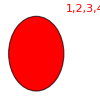
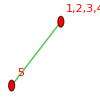
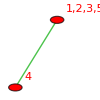
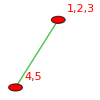
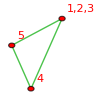
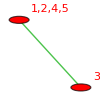
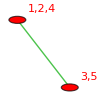
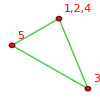
{-Graphics-{59048→v12345,1/6},-Graphics-{58288→v5x1234,1/2},-Graphics-{56770→v4x1235,1/2},-Graphics-{56012→v45x123,1/2},-Graphics-{56011→v4x5x123,1},-Graphics-{52232→v3x1245,1/2},-Graphics-{51478→v35x124,1/2},-Graphics-{51475→v3x5x124,1},-Graphics-{49972→v34x125,1/2},-Graphics-{49963→v3x4x125,1},-Graphics-{49220→v12x345,1/2},-Graphics-{49216→v5x12x34,1},-Graphics-{49210→v4x12x35,1},-Graphics-{49208→v3x12x45,1},-Graphics-{49207→v3x4x5x12,1},-Graphics-{39014→v2x1345,1/2},-Graphics-{38308→v25x134,1/2},-Graphics-{38281→v2x5x134,1},-Graphics-{36898→v24x135,1/2},-Graphics-{36817→v2x4x135,1},-Graphics-{36194→v13x245,1/2},-Graphics-{36166→v5x13x24,1},-Graphics-{36112→v4x13x25,1},-Graphics-{36086→v2x13x45,1},-Graphics-{36085→v2x4x5x13,1},-Graphics-{32684→v23x145,1/2},-Graphics-{32441→v2x3x145,1},-Graphics-{31984→v14x235,1/2},-Graphics-{31954→v5x14x23,1},-Graphics-{31738→v3x14x25,1},-Graphics-{31714→v2x14x35,1},-Graphics-{31711→v2x3x5x14,1},-Graphics-{30586→v15x234,1/2},-Graphics-{30496→v4x15x23,1},-Graphics-{30334→v3x15x24,1},-Graphics-{30262→v2x15x34,1},-Graphics-{30253→v2x3x4x15,1},-Graphics-{29888→v1x2345,1/2},-Graphics-{29857→v1x5x234,1},-Graphics-{29797→v1x4x235,1},-Graphics-{29768→v1x23x45,1},-Graphics-{29767→v1x4x5x23,1},-Graphics-{29633→v1x3x245,1},-Graphics-{29608→v1x24x35,1},-Graphics-{29605→v1x3x5x24,1},-Graphics-{29560→v1x25x34,1},-Graphics-{29551→v1x3x4x25,1},-Graphics-{29537→v1x2x345,1},-Graphics-{29533→v1x2x5x34,1},-Graphics-{29527→v1x2x4x35,1},-Graphics-{29525→v1x2x3x45,1},-Graphics-{29524→v1x2x3x4x5,0}}

```mathematica
Table[CosyPrint5[k],{k,baseKeys5}]
```

```mathematica
graphAssoc5=Table[withComp5[k,"colofour"]->withComp5[k,"graph"],{k,baseKeys5}];
```

```mathematica
Length[graphAssoc5]
```

52

```mathematica
withComp5[29524,"comp"]
```

Equal

## We now replace some of the "b" variables with our greek letters

```mathematica
alfaKey=35977;
betaKey=31681;
gammaKey=23041 ;
deltaKey=20803;
epsilonKey=27259;
alfa1Key=36166;
beta1Key=31738;
gamma1Key=29608;
delta1Key=36112;
epsilon1Key=31714;
lambdaKey=20665;
```

```mathematica
stubbornForm5=withComp5;
```

```mathematica
Keys[stubbornForm5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,compwhy,marked,parents,children}

```mathematica
CosyPrintThree5[key_]:=ColorTablePrint[key,stubbornForm5,"colofour","colortable2"]
```

```mathematica
stubbornKeys=Select[Keys[stubbornForm5],stubbornForm5[#,"comp"]==GreaterEqual&];
```

```mathematica
Length[stubbornKeys]
```

125

```mathematica
stubbornForm5[367,"graph"]
```

-Graphics-

```mathematica
stubbornForm5[7657,"graph"]
```

-Graphics-

```mathematica
stubbornForm5[2554,"graph"]
```

-Graphics-

```mathematica
29608
```

29608

```mathematica
ParentsRecursive[key_,level_]:=Block[
{result={key}}
,
If[level≤0,
{},

Table[
result=Join[result,ParentsRecursive[p,level-1]];
,{p,stubbornForm5[key,"parents"]}
];
DeleteDuplicates[result]
]
]
```

```mathematica
Select[Keys[stubbornForm5],stubbornForm5[#,"comp"]==Greater&&Length[stubbornForm5[#,"parents"]]>1&]//Length
```

1748

```mathematica
nodes=ParentsRecursive[29608,2]
```

{29608,29574,29602,29446,29436,29328,29350,29176,28845,28873,28621,27259,27249,26989,23013,23041,22789,22318,9763,9753,9493,7738}

```mathematica
With[
{g=Graph[Table[Table[p->k,{p,Flatten[stubbornForm5[k,"parents"]]}],{k,nodes}]//Flatten]}
,
Table[l->{stubbornForm5[l,"comp"],If[ToString[stubbornForm5[l,"comp"]]=="GreaterEqual",Red,Green]},{l,VertexList[g]}]
]
```

{29574→{GreaterEqual,RGBColor[1, 0, 0]},29608→{GreaterEqual,RGBColor[1, 0, 0]},29602→{GreaterEqual,RGBColor[1, 0, 0]},29446→{GreaterEqual,RGBColor[1, 0, 0]},29436→{Greater,RGBColor[0, 1, 0]},29328→{Greater,RGBColor[0, 1, 0]},29350→{Greater,RGBColor[0, 1, 0]},29176→{GreaterEqual,RGBColor[1, 0, 0]},28845→{GreaterEqual,RGBColor[1, 0, 0]},28873→{GreaterEqual,RGBColor[1, 0, 0]},28621→{Greater,RGBColor[0, 1, 0]},27259→{Greater,RGBColor[0, 1, 0]},27249→{Greater,RGBColor[0, 1, 0]},26989→{Greater,RGBColor[0, 1, 0]},23013→{Greater,RGBColor[0, 1, 0]},23041→{Greater,RGBColor[0, 1, 0]},22789→{Greater,RGBColor[0, 1, 0]},22318→{GreaterEqual,RGBColor[1, 0, 0]},9763→{GreaterEqual,RGBColor[1, 0, 0]},9753→{Greater,RGBColor[0, 1, 0]},9493→{GreaterEqual,RGBColor[1, 0, 0]},7738→{GreaterEqual,RGBColor[1, 0, 0]},29403→{Greater,RGBColor[0, 1, 0]},29412→{Greater,RGBColor[0, 1, 0]},29322→{Greater,RGBColor[0, 1, 0]},29169→{Greater,RGBColor[0, 1, 0]},27216→{Greater,RGBColor[0, 1, 0]},27225→{Greater,RGBColor[0, 1, 0]},26982→{Greater,RGBColor[0, 1, 0]},9720→{Greater,RGBColor[0, 1, 0]},9729→{Greater,RGBColor[0, 1, 0]},9486→{Greater,RGBColor[0, 1, 0]},7704→{Greater,RGBColor[0, 1, 0]},29430→{Greater,RGBColor[0, 1, 0]},29439→{Greater,RGBColor[0, 1, 0]},29440→{GreaterEqual,RGBColor[1, 0, 0]},29431→{Greater,RGBColor[0, 1, 0]},29413→{Greater,RGBColor[0, 1, 0]},29404→{Greater,RGBColor[0, 1, 0]},29196→{Greater,RGBColor[0, 1, 0]},29197→{Greater,RGBColor[0, 1, 0]},29170→{Greater,RGBColor[0, 1, 0]},27243→{Greater,RGBColor[0, 1, 0]},27252→{Greater,RGBColor[0, 1, 0]},27253→{Greater,RGBColor[0, 1, 0]},27244→{Greater,RGBColor[0, 1, 0]},27226→{Greater,RGBColor[0, 1, 0]},27217→{Greater,RGBColor[0, 1, 0]},27009→{Greater,RGBColor[0, 1, 0]},27010→{Greater,RGBColor[0, 1, 0]},26983→{Greater,RGBColor[0, 1, 0]},9747→{Greater,RGBColor[0, 1, 0]},9756→{Greater,RGBColor[0, 1, 0]},9757→{Greater,RGBColor[0, 1, 0]},9748→{Greater,RGBColor[0, 1, 0]},9730→{Greater,RGBColor[0, 1, 0]},9721→{Greater,RGBColor[0, 1, 0]},9513→{Greater,RGBColor[0, 1, 0]},9514→{Greater,RGBColor[0, 1, 0]},9487→{Greater,RGBColor[0, 1, 0]},7732→{Greater,RGBColor[0, 1, 0]},29188→{Greater,RGBColor[0, 1, 0]},28710→{Greater,RGBColor[0, 1, 0]},28711→{Greater,RGBColor[0, 1, 0]},28702→{Greater,RGBColor[0, 1, 0]},28683→{Greater,RGBColor[0, 1, 0]},28684→{Greater,RGBColor[0, 1, 0]},28675→{Greater,RGBColor[0, 1, 0]},28467→{Greater,RGBColor[0, 1, 0]},28468→{Greater,RGBColor[0, 1, 0]},28459→{Greater,RGBColor[0, 1, 0]},22878→{Greater,RGBColor[0, 1, 0]},22879→{Greater,RGBColor[0, 1, 0]},22870→{Greater,RGBColor[0, 1, 0]},22851→{Greater,RGBColor[0, 1, 0]},22852→{Greater,RGBColor[0, 1, 0]},22843→{Greater,RGBColor[0, 1, 0]},22635→{Greater,RGBColor[0, 1, 0]},22636→{Greater,RGBColor[0, 1, 0]},22627→{Greater,RGBColor[0, 1, 0]},22156→{Greater,RGBColor[0, 1, 0]},29187→{Greater,RGBColor[0, 1, 0]},29166→{Greater,RGBColor[0, 1, 0]},28701→{Greater,RGBColor[0, 1, 0]},28674→{Greater,RGBColor[0, 1, 0]},28458→{Greater,RGBColor[0, 1, 0]},22869→{Greater,RGBColor[0, 1, 0]},22842→{Greater,RGBColor[0, 1, 0]},22626→{Greater,RGBColor[0, 1, 0]},22146→{Greater,RGBColor[0, 1, 0]},28593→{Greater,RGBColor[0, 1, 0]},26979→{Greater,RGBColor[0, 1, 0]},22761→{Greater,RGBColor[0, 1, 0]},22038→{Greater,RGBColor[0, 1, 0]},9483→{Greater,RGBColor[0, 1, 0]},7458→{Greater,RGBColor[0, 1, 0]},29161→{Greater,RGBColor[0, 1, 0]},27000→{Greater,RGBColor[0, 1, 0]},27001→{Greater,RGBColor[0, 1, 0]},26974→{Greater,RGBColor[0, 1, 0]},9504→{Greater,RGBColor[0, 1, 0]},9505→{Greater,RGBColor[0, 1, 0]},9478→{Greater,RGBColor[0, 1, 0]},7480→{Greater,RGBColor[0, 1, 0]},28440→{Greater,RGBColor[0, 1, 0]},28441→{Greater,RGBColor[0, 1, 0]},28432→{Greater,RGBColor[0, 1, 0]},22608→{Greater,RGBColor[0, 1, 0]},22609→{Greater,RGBColor[0, 1, 0]},22600→{Greater,RGBColor[0, 1, 0]},21886→{Greater,RGBColor[0, 1, 0]},26487→{Greater,RGBColor[0, 1, 0]},26496→{Greater,RGBColor[0, 1, 0]},26253→{Greater,RGBColor[0, 1, 0]},22284→{Greater,RGBColor[0, 1, 0]},8991→{Greater,RGBColor[0, 1, 0]},9000→{Greater,RGBColor[0, 1, 0]},8757→{Greater,RGBColor[0, 1, 0]},6975→{Greater,RGBColor[0, 1, 0]},26514→{Greater,RGBColor[0, 1, 0]},26523→{Greater,RGBColor[0, 1, 0]},26524→{Greater,RGBColor[0, 1, 0]},26515→{Greater,RGBColor[0, 1, 0]},26497→{Greater,RGBColor[0, 1, 0]},26488→{Greater,RGBColor[0, 1, 0]},26280→{Greater,RGBColor[0, 1, 0]},26281→{Greater,RGBColor[0, 1, 0]},26254→{Greater,RGBColor[0, 1, 0]},22312→{Greater,RGBColor[0, 1, 0]},9018→{Greater,RGBColor[0, 1, 0]},9027→{Greater,RGBColor[0, 1, 0]},9028→{Greater,RGBColor[0, 1, 0]},9019→{Greater,RGBColor[0, 1, 0]},9001→{Greater,RGBColor[0, 1, 0]},8992→{Greater,RGBColor[0, 1, 0]},8784→{Greater,RGBColor[0, 1, 0]},8785→{Greater,RGBColor[0, 1, 0]},8758→{Greater,RGBColor[0, 1, 0]},7003→{Greater,RGBColor[0, 1, 0]},26271→{Greater,RGBColor[0, 1, 0]},26272→{Greater,RGBColor[0, 1, 0]},26245→{Greater,RGBColor[0, 1, 0]},22060→{Greater,RGBColor[0, 1, 0]},8775→{Greater,RGBColor[0, 1, 0]},8776→{Greater,RGBColor[0, 1, 0]},8749→{Greater,RGBColor[0, 1, 0]},6751→{Greater,RGBColor[0, 1, 0]},20691→{Greater,RGBColor[0, 1, 0]},20692→{Greater,RGBColor[0, 1, 0]},20683→{Greater,RGBColor[0, 1, 0]},20664→{Greater,RGBColor[0, 1, 0]},20665→{Greater,RGBColor[0, 1, 0]},20656→{Greater,RGBColor[0, 1, 0]},20448→{Greater,RGBColor[0, 1, 0]},20449→{Greater,RGBColor[0, 1, 0]},20440→{Greater,RGBColor[0, 1, 0]},19969→{Greater,RGBColor[0, 1, 0]},7576→{Greater,RGBColor[0, 1, 0]},20682→{Greater,RGBColor[0, 1, 0]},20655→{Greater,RGBColor[0, 1, 0]},20439→{Greater,RGBColor[0, 1, 0]},19959→{Greater,RGBColor[0, 1, 0]},7566→{Greater,RGBColor[0, 1, 0]},20421→{Greater,RGBColor[0, 1, 0]},20422→{Greater,RGBColor[0, 1, 0]},20413→{Greater,RGBColor[0, 1, 0]},19699→{Greater,RGBColor[0, 1, 0]},7306→{Greater,RGBColor[0, 1, 0]},3159→{Greater,RGBColor[0, 1, 0]},3168→{Greater,RGBColor[0, 1, 0]},2925→{Greater,RGBColor[0, 1, 0]},1143→{Greater,RGBColor[0, 1, 0]},3186→{Greater,RGBColor[0, 1, 0]},3195→{Greater,RGBColor[0, 1, 0]},3196→{Greater,RGBColor[0, 1, 0]},3187→{Greater,RGBColor[0, 1, 0]},3169→{Greater,RGBColor[0, 1, 0]},3160→{Greater,RGBColor[0, 1, 0]},2952→{Greater,RGBColor[0, 1, 0]},2953→{Greater,RGBColor[0, 1, 0]},2926→{Greater,RGBColor[0, 1, 0]},1171→{Greater,RGBColor[0, 1, 0]},2943→{Greater,RGBColor[0, 1, 0]},2944→{Greater,RGBColor[0, 1, 0]},2917→{Greater,RGBColor[0, 1, 0]},919→{Greater,RGBColor[0, 1, 0]},2473→{Greater,RGBColor[0, 1, 0]},2463→{Greater,RGBColor[0, 1, 0]},2203→{Greater,RGBColor[0, 1, 0]},448→{GreaterEqual,RGBColor[1, 0, 0]}}

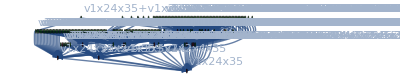

```mathematica
With[
{g=Graph[Table[Table[p->k,{p,Flatten[stubbornForm5[k,"parents"]]}],{k,nodes}]//Flatten]}
,
Graph[VertexList[g],EdgeList[g],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top},
VertexLabels->Table[l->stubbornForm5[l,"colofour"],{l,VertexList[g]}](*Table[k->stubbornForm5[k,"colofour"],{k,Take[stubbornKeys,8]}]*),
VertexStyle->Table[l->If[ToString[stubbornForm5[l,"comp"]]=="GreaterEqual",Red,Green],{l,VertexList[g]}]]
]
```

```mathematica
ineqsthree5=Table[stubbornForm5[k]["comp"][stubbornForm5[k]["colofour"],0],{k,Keys[stubbornForm5]}]//Simplify;
```

```mathematica
Take[ineqsthree5,5]
```

{v12345+v12x345+v13x245+v14x235+v15x234+v1x2345+v1x23x45+v1x24x35+v1x25x34+v1x2x345+v1x2x3x45+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v23x145+v24x135+v25x134+v2x1345+v2x13x45+v2x14x35+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v34x125+v35x124+v3x1245+v3x12x45+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v45x123+v4x1235+v4x12x35+v4x13x25+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23>0,v14x235+v15x234+v1x24x35+v1x25x34+v1x2x3x4x5+v1x2x4x35+v1x2x5x34+v1x3x4x25+v1x3x5x24+v1x4x235+v1x4x5x23+v1x5x234+v24x135+v25x134+v2x14x35+v2x15x34+v2x3x4x15+v2x3x5x14+v2x4x135+v2x4x5x13+v2x5x134+v34x125+v35x124+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v4x1235+v4x12x35+v4x13x25+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23>0,v12345+v12x345+v13x245+v1x2345+v1x23x45+v1x2x345+v1x2x3x45+v1x3x245+v23x145+v2x1345+v2x13x45+v2x3x145+v3x1245+v3x12x45+v45x123>0,v13x245+v15x234+v1x23x45+v1x25x34+v1x2x3x45+v1x2x3x4x5+v1x2x5x34+v1x3x245+v1x3x4x25+v1x3x5x24+v1x4x5x23+v1x5x234+v23x145+v25x134+v2x13x45+v2x15x34+v2x3x145+v2x3x4x15+v2x3x5x14+v2x4x5x13+v2x5x134+v34x125+v3x1245+v3x12x45+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v45x123+v4x13x25+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23>0,v15x234+v1x25x34+v1x2x3x4x5+v1x2x5x34+v1x3x4x25+v1x3x5x24+v1x4x5x23+v1x5x234+v25x134+v2x15x34+v2x3x4x15+v2x3x5x14+v2x4x5x13+v2x5x134+v34x125+v3x14x25+v3x15x24+v3x4x125+v3x4x5x12+v3x5x124+v4x13x25+v4x15x23+v4x5x123+v5x1234+v5x12x34+v5x13x24+v5x14x23>0}

```mathematica
ineqsthree52=Simplify[Fold[And,ineqsthree5]];Length[ineqsthree52]
```

72

```mathematica
Take[ineqsthree52,5]
```

v12345>0&&v12x345>0&&v13x245≥0&&v14x235≥0&&v15x234>0

```mathematica
Fold[And,Table[stubbornForm5[k,"colofour"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]
```

v5x13x24==0&&v3x14x25==0&&v1x24x35==0&&v4x13x25==0&&v2x14x35==0

```mathematica
simp=Simplify[ineqsthree52&&v5x13x24==0&&v3x14x25==0&&v1x24x35==0&&v4x13x25==0&&v2x14x35==0&&
v3x5x124>0&&v35x124>0&&v2x5x134>0&&v25x134>0&&v2x4x135>0&&v24x135>0&&v1x4x235>0&&v1x3x245>0&&v14x235>0&&v14x235>0&&v13x245>0&&v5x14x23>0&&v3x15x24>0&&v1x25x34>0&&v4x12x35>0&&v2x13x45>0]
```

v12345>0&&v12x345>0&&v13x245>0&&v14x235>0&&v15x234>0&&v1x2345>0&&v1x23x45>0&&v1x24x35==0&&v1x25x34>0&&v1x2x345>0&&v1x2x3x45>0&&v1x2x4x35>0&&v1x2x5x34>0&&v1x3x245>0&&v1x3x4x25>0&&v1x3x5x24>0&&v1x4x235>0&&v1x4x5x23>0&&v1x5x234>0&&v23x145>0&&v24x135>0&&v25x134>0&&v2x1345>0&&v2x13x45>0&&v2x14x35==0&&v2x15x34>0&&v2x3x145>0&&v2x3x4x15>0&&v2x3x5x14>0&&v2x4x135>0&&v2x4x5x13>0&&v2x5x134>0&&v34x125>0&&v35x124>0&&v3x1245>0&&v3x12x45>0&&v3x14x25==0&&v3x15x24>0&&v3x4x125>0&&v3x4x5x12>0&&v3x5x124>0&&v45x123>0&&v4x1235>0&&v4x12x35>0&&v4x13x25==0&&v4x15x23>0&&v4x5x123>0&&v5x1234>0&&v5x12x34>0&&v5x13x24==0&&v5x14x23>0&&v1x2x3x4x5==0

```mathematica
ExpressionToTable[simp]
```

v4x5x123>0
v45x123>0
v3x5x124>0
v35x124>0
v3x4x125>0
v34x125>0
v2x5x134>0
v25x134>0
v2x4x135>0
v24x135>0
v2x3x145>0
v23x145>0
v5x1234>0
v1x5x234>0
v15x234>0
v4x1235>0
v1x4x235>0
v14x235>0
v3x1245>0
v1x3x245>0
v13x245>0
v2x1345>0
v1x2x345>0
v1x2345>0
v12x345>0
v12345>0
v1x2x3x4x5==0
v3x4x5x12>0
v2x4x5x13>0
v2x3x5x14>0
v2x3x4x15>0
v5x14x23>0
v4x15x23>0
v1x4x5x23>0
v3x15x24>0
v1x3x5x24>0
v5x13x24==0
v1x3x4x25>0
v4x13x25==0
v3x14x25==0
v5x12x34>0
v2x15x34>0
v1x2x5x34>0
v1x25x34>0
v4x12x35>0
v1x2x4x35>0
v2x14x35==0
v1x24x35==0
v3x12x45>0
v1x2x3x45>0
v1x23x45>0
v2x13x45==0

```mathematica
IsGoodKey2[key_]:=Block[{result=False},If[ToString[stubbornForm5[key,"comp"]]=="Greater",Table[If[ToString[stubbornForm5[childcouple[[1]],"comp"]]=="GreaterEqual"&&ToString[stubbornForm5[childcouple[[2]],"comp"]]=="GreaterEqual",result=True;],{childcouple,stubbornForm5[key,"children"]}];
result,False]]
```

```mathematica
CollectThem[key_]:=Block[{result={}},If[ToString[stubbornForm5[key,"comp"]]=="Greater",Table[If[ToString[stubbornForm5[childcouple[[1]],"comp"]]=="GreaterEqual"&&ToString[stubbornForm5[childcouple[[2]],"comp"]]=="GreaterEqual",
result=Join[result,{key->childcouple[[1]],key->childcouple[[2]]}];],{childcouple,stubbornForm5[key,"children"]}];
result,{}]]
```

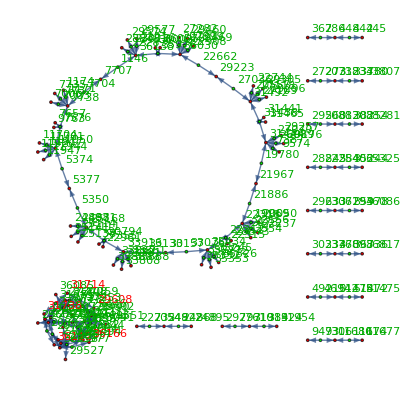

```mathematica
hhh=With[
{g=Graph[Flatten[Table[CollectThem[k],{k,Keys[stubbornForm5]}]],GraphLayout->"RadialDrawing"]}
,
Graph[VertexList[g],EdgeList[g],
VertexLabels->Table[l->Style[l,If[MemberQ[{29608,36166,36112,31714,31738},l],Red,Darker[Green]]],{l,VertexList[g]}](*Table[k->stubbornForm5[k,"colofour"],{k,Take[stubbornKeys,8]}]*),
VertexStyle->Table[l->If[ToString[stubbornForm5[l,"comp"]]=="GreaterEqual",Red,Green],{l,VertexList[g]}]]
]
```

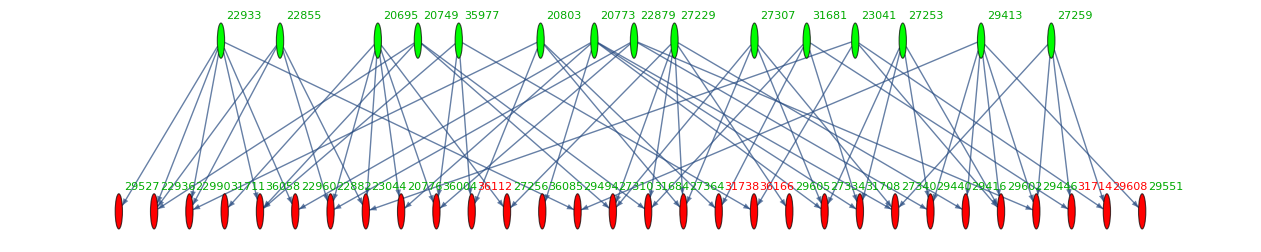

```mathematica
With[
{g=NeighborhoodGraph[hhh,22933,30]}
,
Graph[VertexList[g],EdgeList[g],
VertexLabels->Table[l->Style[l,If[MemberQ[{29608,36166,36112,31714,31738},l],Red,Darker[Green]]],{l,VertexList[g]}],
GraphLayout->"LayeredDigraphEmbedding"
(*Table[k->stubbornForm5[k,"colofour"],{k,Take[stubbornKeys,8]}]*),
VertexStyle->Table[l->If[ToString[stubbornForm5[l,"comp"]]=="GreaterEqual",Red,Green],{l,VertexList[g]}]]
]
```

45

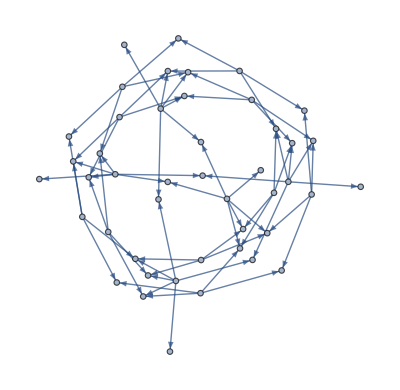

```mathematica
VertexCount[NeighborhoodGraph[hhh,22933,30]]
```

```mathematica
FindSpanningTree
```

```mathematica
Length[stubbornForm5]
```

1895

## Define some of graphs that have additional nodes

```mathematica
Clear[sixNodes]
```

```mathematica
sixNodes=stubbornForm5;
```

```mathematica
DefineNew[newKey_,key1_,key2_,graph_,operation_:Plus]:=Block[{first=sixNodes[key1], second=sixNodes[key2], newEntry},
newEntry=Association[];
newEntry["signature"]=newKey;
Table[
newEntry[key]=Simplify[operation[first[key],second[key]]]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["relations"]={Symbol["x"<>ToString[newKey]]==operation[Symbol["x"<>ToString[key1]],Symbol["x"<>ToString[key2]]]};
newEntry["graph"]=graph;
newEntry
]
```

```mathematica
double1Key=29413;
double2Key=20773;
double3Key=27229;
double4Key=22933;
double5Key=20695;
single13Key=27226;
single24Key=20746;
single35Key=20668;
single41Key=22852;
single52Key=20692;
```

```mathematica
sixPositions=Append[N[MyCircle[{{1},{2},{3},{4},{5}},5]],{0,0}];
```

```mathematica
DefineFull[]:=Block[{empty = sixNodes[lambdaKey],amigo1=sixNodes[double1Key], amigo2=sixNodes[double5Key],amigo3=sixNodes[single24Key], newEntry},
newEntry=Association[];
newEntry["signature"]="full";
Table[
newEntry[key]=Simplify[2*empty[key]-(amigo1[key]+amigo2[key]+amigo3[key])]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["matrix"]=empty["matrix"];
newEntry["graph"]=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,3<->6,4<->6,5<->6},VertexLabels->"Name",VertexSize->Normal,
ImageSize->{50,50},VertexCoordinates->sixPositions];
newEntry["vertexsets"]=empty["vertexsets"];
newEntry["vertices"]=empty["vertices"];
newEntry["relations"]={};
newEntry
]
```

```mathematica
DefineFull[]
```

<|signature→full,colofour→v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25+v5x13x24,colortable→{{0,v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25+v5x13x24},{v4x13x25+v5x13x24,v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25},{v2x14x35+v3x14x25,v1x24x35-v1x2x3x4x5+v4x13x25+v5x13x24},{0,v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25+v5x13x24},{0,v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25+v5x13x24},{v1x24x35+v5x13x24,-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25},{v3x14x25+v4x13x25,v1x24x35-v1x2x3x4x5+v2x14x35+v5x13x24},{0,v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25+v5x13x24},{v1x24x35+v2x14x35,-v1x2x3x4x5+v3x14x25+v4x13x25+v5x13x24},{0,v1x24x35-v1x2x3x4x5+v2x14x35+v3x14x25+v4x13x25+v5x13x24}},comp→GreaterEqual,matrix→{{2,1,0,0,1},{1,2,1,0,0},{0,1,2,1,0},{0,0,1,2,1},{1,0,0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},relations→{}|>

```mathematica
sixNodes["full"]=DefineFull[];
```

```mathematica
(sixNodes["B43","colortable"]/.{v1x2x3x4x5->0,v5x13x24->0,v3x14x25->0,v1x24x35->0,v4x13x25->0,v2x14x35->0}/.graphAssoc5)//MatrixForm
```

(0 | -Graphics-+-Graphics-
0 | -Graphics-+-Graphics-
0 | -Graphics-+-Graphics-
0 | -Graphics-+-Graphics-
0 | -Graphics-+-Graphics-
-Graphics- | -Graphics-
0 | -Graphics-+-Graphics-
0 | -Graphics-+-Graphics-
-Graphics- | -Graphics-
0 | -Graphics-+-Graphics-)

```mathematica
(sixNodes["full","colortable"]/.{v1x2x3x4x5->0}/.graphAssoc5)//MatrixForm
```

(0 | -Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-+-Graphics- | -Graphics-+-Graphics-+-Graphics-
-Graphics-+-Graphics- | -Graphics-+-Graphics-+-Graphics-
0 | -Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
0 | -Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-+-Graphics- | -Graphics-+-Graphics-+-Graphics-
-Graphics-+-Graphics- | -Graphics-+-Graphics-+-Graphics-
0 | -Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-+-Graphics- | -Graphics-+-Graphics-+-Graphics-
0 | -Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-)

```mathematica
sixNodes["B43","graph"]
```

-Graphics-

```mathematica
Select[Keys[sixNodes],sixNodes[#,"colofour"]==v1x2x3x4x5&]
```

{29524}

```mathematica
sixNodes[29524]
```

<|signature→29524,matrix→{{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},relations→{x29524==-x49207+x9841,x29524==x22963-x36085,x29524==x27337-x31711,x29524==x28795-x30253,x29524==x29281-x29767,x29524==x29443-x29605,x29524==x29497-x29551,x29524==x29515-x29533,x29524==x29521-x29527,x29524==x29523-x29525},links→{},colofour→v1x2x3x4x5,colortable→{{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5}},colortable2→{{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5}},comp→Equal,marked→True,parents→{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841},children→{},compWHY→Planar contraction,compwhy→Contains K Five|>

```mathematica
Clear[sixNodes]
```

#### 1 spike missing

```mathematica
sixNodes["B18"]=DefineNew["B18",double1Key,"full",EdgeDelete[sixNodes["full","graph"],{1<->6}]];
```

```mathematica
sixNodes["B19"]=DefineNew["B19",double2Key,"full",EdgeDelete[sixNodes["full","graph"],{2<->6}]];
```

```mathematica
sixNodes["B20"]=DefineNew["B20",double3Key,"full",EdgeDelete[sixNodes["full","graph"],{3<->6}]];
```

```mathematica
sixNodes["B21"]=DefineNew["B21",double4Key,"full",EdgeDelete[sixNodes["full","graph"],{4<->6}]];
```

```mathematica
sixNodes["B22"]=DefineNew["B22",double5Key,"full",EdgeDelete[sixNodes["full","graph"],{5<->6}]];
```

#### 2 spikes missing

```mathematica
sixNodes["B23"]=DefineNew["B23","full","B18",EdgeDelete[sixNodes["B18","graph"],{2<->6}]];
```

```mathematica
sixNodes["B24"]=DefineNew["B24","full","B19",EdgeDelete[sixNodes["B19","graph"],{3<->6}]];
```

```mathematica
sixNodes["B25"]=DefineNew["B25","full","B20",EdgeDelete[sixNodes["B20","graph"],{4<->6}]];
```

```mathematica
sixNodes["B26"]=DefineNew["B26","full","B21",EdgeDelete[sixNodes["B21","graph"],{5<->6}]];
```

```mathematica
sixNodes["B27"]=DefineNew["B27","full","B22",EdgeDelete[sixNodes["B22","graph"],{1<->6}]];
```

#### Full with one spike in other direction

```mathematica
sixNodes["B43"]=DefineNew["B43","B18",deltaKey,EdgeAdd[sixNodes["B18","graph"],{2<->5}],Subtract];
```

```mathematica
(*sixNodes["B43","comp"]=Greater;sixNodes["B43","compwhy"]="Obvious from colofour";*)
```

```mathematica
sixNodes["B44"]=DefineNew["B44","B19",alfaKey,EdgeAdd[sixNodes["B19","graph"],{1<->3}],Subtract];
```

```mathematica
(*sixNodes["B44","comp"]=Greater;sixNodes["B44","compwhy"]="Obvious from colofour";*)
```

```mathematica
sixNodes["B45"]=DefineNew["B45","B20",gammaKey,EdgeAdd[sixNodes["B20","graph"],{2<->4}],Subtract];
```

```mathematica
(*sixNodes["B45","comp"]=Greater;sixNodes["B45","compwhy"]="Obvious from colofour";*)
```

```mathematica
sixNodes["B46"]=DefineNew["B46","B21",epsilonKey,EdgeAdd[sixNodes["B21","graph"],{3<->5}],Subtract];
```

```mathematica
(*sixNodes["B46","comp"]=Greater;sixNodes["B46","compwhy"]="Obvious from colofour";*)
```

```mathematica
sixNodes["B47"]=DefineNew["B47","B22",betaKey,EdgeAdd[sixNodes["B22","graph"],{1<->4}],Subtract];
```

```mathematica
(*sixNodes["B47","comp"]=Greater;sixNodes["B47","compwhy"]="Obvious from colofour";*)
```

```mathematica
CountCompGreaterEqual[assoc_]:=Select[Keys[assoc],ToString[assoc[#]["comp"]]=="GreaterEqual"&]//Length
```

```mathematica
GetCompSix[key_]:=Block[{},sixNodes[key]]
```

```mathematica
SetCompSix[key_,value_]:=Block[{},sixNodes[key]=value]
```

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

PropagateComp[GetCompSix,SetCompSix,{0,1,2,3,4,6,9,10,12,13,14,16,18,22,26,27,28,30,31,36,37,39,40,45,49,54,63,72,81,82,84,85,87,90,91,93,94,97,108,109,110,111,112,117,118,120,121,122,136,145,162,165,168,190,193,218,243,244,245,246,247,252,253,255,256,257,270,271,273,274,276,279,280,282,283,286,300,309,324,325,327,328,333,334,336,337,342,346,351,352,353,354,355,357,360,361,363,364,365,367,369,373,377,382,391,400,414,417,442,445,448,473,486,487,488,516,517,546,576,577,606,607,608,637,666,697,728,729,730,732,733,738,739,741,742,747,751,756,757,759,760,765,766,768,769,774,778,810,811,813,814,819,820,822,823,837,838,840,841,846,847,849,850,891,894,919,922,972,973,975,976,981,982,984,985,999,1000,1002,1003,1008,1009,1011,1012,1053,1054,1056,1057,1062,1063,1065,1066,1071,1075,1080,1081,1083,1084,1089,1090,1092,1093,1098,1102,1143,1146,1171,1174,1215,1216,1245,1246,1305,1306,1335,1336,1395,1426,1458,1467,1476,1539,1548,1620,1701,1710,1782,1791,1800,1872,1944,2034,2124,2187,2188,2190,2191,2193,2196,2197,2199,2200,2203,2214,2215,2217,2218,2223,2224,2226,2227,2241,2250,2268,2269,2271,2272,2274,2277,2278,2280,2281,2284,2295,2296,2298,2299,2304,2305,2307,2308,2323,2332,2430,2431,2433,2434,2439,2440,2442,2443,2457,2458,2460,2461,2463,2466,2467,2469,2470,2473,2487,2496,2511,2512,2514,2515,2520,2521,2523,2524,2538,2539,2541,2542,2544,2547,2548,2550,2551,2554,2569,2578,2673,2674,2703,2704,2733,2763,2764,2793,2794,2824,2916,2917,2918,2919,2920,2925,2926,2928,2929,2930,2943,2944,2946,2947,2952,2953,2955,2956,2997,2998,3000,3001,3006,3007,3009,3010,3024,3025,3026,3027,3028,3033,3034,3036,3037,3038,3159,3160,3161,3162,3163,3168,3169,3171,3172,3173,3186,3187,3189,3190,3195,3196,3198,3199,3240,3241,3243,3244,3249,3250,3252,3253,3267,3268,3269,3270,3271,3276,3277,3279,3280,3281,3402,3403,3404,3432,3433,3492,3493,3522,3523,3524,3646,3655,3727,3736,3889,3898,3970,3979,4132,4222,4374,4377,4380,4401,4404,4428,4617,4620,4644,4647,4650,4674,4860,4890,4920,5104,5107,5131,5134,5347,5350,5374,5377,5590,5620,5834,6077,6320,6561,6562,6563,6564,6565,6570,6571,6573,6574,6575,6588,6589,6591,6592,6597,6598,6600,6601,6615,6624,6642,6643,6645,6646,6651,6652,6654,6655,6669,6670,6671,6672,6673,6678,6679,6681,6682,6683,6697,6706,6723,6726,6751,6754,6779,6804,6805,6806,6807,6808,6813,6814,6816,6817,6818,6831,6832,6834,6835,6840,6841,6843,6844,6861,6870,6885,6886,6888,6889,6894,6895,6897,6898,6912,6913,6914,6915,6916,6921,6922,6924,6925,6926,6943,6952,6975,6978,7003,7006,7034,7290,7291,7293,7294,7296,7299,7300,7302,7303,7306,7317,7318,7320,7321,7326,7327,7329,7330,7371,7372,7374,7375,7377,7380,7381,7383,7384,7387,7398,7399,7401,7402,7407,7408,7410,7411,7452,7455,7458,7480,7483,7533,7534,7536,7537,7542,7543,7545,7546,7560,7561,7563,7564,7566,7569,7570,7572,7573,7576,7614,7615,7617,7618,7623,7624,7626,7627,7641,7642,7644,7645,7647,7650,7651,7653,7654,7657,7704,7707,7732,7735,7738,8022,8031,8103,8112,8184,8265,8274,8346,8355,8436,8748,8749,8751,8752,8757,8758,8760,8761,8766,8770,8775,8776,8778,8779,8784,8785,8787,8788,8793,8797,8802,8811,8820,8829,8830,8832,8833,8838,8839,8841,8842,8856,8857,8859,8860,8865,8866,8868,8869,8884,8893,8991,8992,8994,8995,9000,9001,9003,9004,9018,9019,9021,9022,9027,9028,9030,9031,9048,9057,9072,9073,9075,9076,9081,9082,9084,9085,9090,9094,9099,9100,9102,9103,9108,9109,9111,9112,9117,9121,9130,9139,9148,9477,9478,9479,9480,9481,9483,9486,9487,9489,9490,9491,9493,9495,9499,9503,9504,9505,9507,9508,9513,9514,9516,9517,9522,9526,9558,9559,9561,9562,9564,9567,9568,9570,9571,9574,9585,9586,9587,9588,9589,9594,9595,9597,9598,9599,9720,9721,9722,9723,9724,9729,9730,9732,9733,9734,9747,9748,9750,9751,9753,9756,9757,9759,9760,9763,9801,9802,9804,9805,9810,9811,9813,9814,9819,9823,9828,9829,9830,9831,9832,9834,9837,9838,9840,9841,9842,9844,9846,9850,9854,10210,10219,10228,10291,10300,10453,10462,10534,10543,10552,10944,10947,10971,10974,10998,11187,11190,11214,11217,11244,11674,11677,11680,11701,11704,11917,11920,11944,11947,11950,12407,12650,13122,13123,13124,13149,13150,13176,13203,13204,13230,13231,13232,13258,13284,13312,13340,13854,13855,13881,13882,13935,13936,13962,13963,14016,14044,14586,14667,14748,15318,15319,15345,15346,15372,15399,15400,15426,15427,15454,16050,16051,16052,16077,16078,16131,16132,16158,16159,16160,16783,16864,17514,17541,17568,18247,18274,18980,19683,19684,19685,19686,19687,19689,19692,19693,19695,19696,19697,19699,19701,19705,19709,19710,19711,19713,19714,19719,19720,19722,19723,19728,19732,19764,19765,19767,19768,19770,19773,19774,19776,19777,19780,19791,19792,19793,19794,19795,19800,19801,19803,19804,19805,19926,19927,19928,19929,19930,19935,19936,19938,19939,19940,19953,19954,19956,19957,19959,19962,19963,19965,19966,19969,20007,20008,20010,20011,20016,20017,20019,20020,20025,20029,20034,20035,20036,20037,20038,20040,20043,20044,20046,20047,20048,20050,20052,20056,20060,20412,20413,20415,20416,20421,20422,20424,20425,20430,20434,20439,20440,20442,20443,20448,20449,20451,20452,20457,20461,20466,20475,20484,20493,20494,20496,20497,20502,20503,20505,20506,20520,20521,20523,20524,20529,20530,20532,20533,20548,20557,20655,20656,20658,20659,20664,20665,20667,20668,20682,20683,20685,20686,20691,20692,20694,20695,20712,20721,20736,20737,20739,20740,20745,20746,20748,20749,20754,20758,20763,20764,20766,20767,20772,20773,20775,20776,20781,20785,20794,20803,20812,21168,21177,21186,21249,21258,21411,21420,21492,21501,21510,21870,21871,21873,21874,21876,21879,21880,21882,21883,21886,21897,21898,21900,21901,21906,21907,21909,21910,21951,21952,21954,21955,21957,21960,21961,21963,21964,21967,21978,21979,21981,21982,21987,21988,21990,21991,22032,22035,22038,22060,22063,22113,22114,22116,22117,22122,22123,22125,22126,22140,22141,22143,22144,22146,22149,22150,22152,22153,22156,22194,22195,22197,22198,22203,22204,22206,22207,22221,22222,22224,22225,22227,22230,22231,22233,22234,22237,22284,22287,22312,22315,22318,22599,22600,22601,22602,22603,22608,22609,22611,22612,22613,22626,22627,22629,22630,22635,22636,22638,22639,22653,22662,22680,22681,22683,22684,22689,22690,22692,22693,22707,22708,22709,22710,22711,22716,22717,22719,22720,22721,22735,22744,22761,22764,22789,22792,22817,22842,22843,22844,22845,22846,22851,22852,22854,22855,22856,22869,22870,22872,22873,22878,22879,22881,22882,22899,22908,22923,22924,22926,22927,22932,22933,22935,22936,22950,22951,22952,22953,22954,22959,22960,22962,22963,22964,22981,22990,23013,23016,23041,23044,23072,23356,23365,23437,23446,23518,23599,23608,23680,23689,23770,24138,24141,24144,24165,24168,24381,24384,24408,24411,24414,24868,24871,24895,24898,24922,25111,25114,25138,25141,25168,25625,25868,26244,26245,26246,26247,26248,26253,26254,26256,26257,26258,26271,26272,26274,26275,26280,26281,26283,26284,26325,26326,26328,26329,26334,26335,26337,26338,26352,26353,26354,26355,26356,26361,26362,26364,26365,26366,26487,26488,26489,26490,26491,26496,26497,26499,26500,26501,26514,26515,26517,26518,26523,26524,26526,26527,26568,26569,26571,26572,26577,26578,26580,26581,26595,26596,26597,26598,26599,26604,26605,26607,26608,26609,26730,26731,26732,26760,26761,26820,26821,26850,26851,26852,26973,26974,26976,26977,26979,26982,26983,26985,26986,26989,27000,27001,27003,27004,27009,27010,27012,27013,27027,27036,27054,27055,27057,27058,27060,27063,27064,27066,27067,27070,27081,27082,27084,27085,27090,27091,27093,27094,27109,27118,27216,27217,27219,27220,27225,27226,27228,27229,27243,27244,27246,27247,27249,27252,27253,27255,27256,27259,27273,27282,27297,27298,27300,27301,27306,27307,27309,27310,27324,27325,27327,27328,27330,27333,27334,27336,27337,27340,27355,27364,27459,27460,27489,27490,27519,27549,27550,27579,27580,27610,27732,27741,27813,27822,27975,27984,28056,28065,28218,28308,28431,28432,28434,28435,28440,28441,28443,28444,28449,28453,28458,28459,28461,28462,28467,28468,28470,28471,28476,28480,28512,28513,28515,28516,28521,28522,28524,28525,28539,28540,28542,28543,28548,28549,28551,28552,28593,28596,28621,28624,28674,28675,28677,28678,28683,28684,28686,28687,28701,28702,28704,28705,28710,28711,28713,28714,28755,28756,28758,28759,28764,28765,28767,28768,28773,28777,28782,28783,28785,28786,28791,28792,28794,28795,28800,28804,28845,28848,28873,28876,28917,28918,28947,28948,29007,29008,29037,29038,29097,29128,29160,29161,29162,29163,29164,29166,29169,29170,29172,29173,29174,29176,29178,29182,29186,29187,29188,29190,29191,29196,29197,29199,29200,29205,29209,29214,29223,29232,29241,29242,29244,29245,29247,29250,29251,29253,29254,29257,29268,29269,29270,29271,29272,29277,29278,29280,29281,29282,29296,29305,29322,29325,29328,29350,29353,29378,29403,29404,29405,29406,29407,29412,29413,29415,29416,29417,29430,29431,29433,29434,29436,29439,29440,29442,29443,29446,29460,29469,29484,29485,29487,29488,29493,29494,29496,29497,29502,29506,29511,29512,29513,29514,29515,29517,29520,29521,29523,29524,29525,29527,29529,29533,29537,29542,29551,29560,29574,29577,29602,29605,29608,29633,29646,29647,29648,29676,29677,29706,29736,29737,29766,29767,29768,29797,29826,29857,29888,29920,29929,29938,30001,30010,30082,30163,30172,30244,30253,30262,30334,30406,30496,30586,30708,30711,30735,30738,30951,30954,30978,30981,31194,31224,31438,31441,31444,31465,31468,31492,31681,31684,31708,31711,31714,31738,31924,31954,31984,32198,32441,32684,33048,33049,33050,33075,33076,33129,33130,33156,33157,33158,33780,33781,33807,33808,33834,33861,33862,33888,33889,33916,34539,34620,35244,35245,35271,35272,35325,35326,35352,35353,35406,35434,35976,35977,35978,36003,36004,36030,36057,36058,36084,36085,36086,36112,36138,36166,36194,36736,36817,36898,37521,37548,38254,38281,38308,39014,39366,39367,39368,39369,39370,39372,39375,39376,39378,39379,39380,39382,39384,39388,39392,40122,40123,40125,40126,40131,40132,40134,40135,40140,40144,40878,40887,40896,41634,41635,41637,41638,41640,41643,41644,41646,41647,41650,42390,42391,42392,42393,42394,42399,42400,42402,42403,42404,43147,43156,43902,43905,43908,44659,44662,45416,46170,46171,46172,46173,46174,46179,46180,46182,46183,46184,46926,46927,46929,46930,46932,46935,46936,46938,46939,46942,47685,47694,48438,48439,48441,48442,48447,48448,48450,48451,48456,48460,49194,49195,49196,49197,49198,49200,49203,49204,49206,49207,49208,49210,49212,49216,49220,49954,49963,49972,50715,50718,51472,51475,51478,52232,52974,52975,52976,53733,53734,54492,55251,55252,56010,56011,56012,56770,57528,58288,59048,full,B18,B19,B20,B21,B22,B23,B24,B25,B26,B27,B43,B44,B45,B46,B47}]

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

PropagateComp[GetCompSix,SetCompSix,{0,1,2,3,4,6,9,10,12,13,14,16,18,22,26,27,28,30,31,36,37,39,40,45,49,54,63,72,81,82,84,85,87,90,91,93,94,97,108,109,110,111,112,117,118,120,121,122,136,145,162,165,168,190,193,218,243,244,245,246,247,252,253,255,256,257,270,271,273,274,276,279,280,282,283,286,300,309,324,325,327,328,333,334,336,337,342,346,351,352,353,354,355,357,360,361,363,364,365,367,369,373,377,382,391,400,414,417,442,445,448,473,486,487,488,516,517,546,576,577,606,607,608,637,666,697,728,729,730,732,733,738,739,741,742,747,751,756,757,759,760,765,766,768,769,774,778,810,811,813,814,819,820,822,823,837,838,840,841,846,847,849,850,891,894,919,922,972,973,975,976,981,982,984,985,999,1000,1002,1003,1008,1009,1011,1012,1053,1054,1056,1057,1062,1063,1065,1066,1071,1075,1080,1081,1083,1084,1089,1090,1092,1093,1098,1102,1143,1146,1171,1174,1215,1216,1245,1246,1305,1306,1335,1336,1395,1426,1458,1467,1476,1539,1548,1620,1701,1710,1782,1791,1800,1872,1944,2034,2124,2187,2188,2190,2191,2193,2196,2197,2199,2200,2203,2214,2215,2217,2218,2223,2224,2226,2227,2241,2250,2268,2269,2271,2272,2274,2277,2278,2280,2281,2284,2295,2296,2298,2299,2304,2305,2307,2308,2323,2332,2430,2431,2433,2434,2439,2440,2442,2443,2457,2458,2460,2461,2463,2466,2467,2469,2470,2473,2487,2496,2511,2512,2514,2515,2520,2521,2523,2524,2538,2539,2541,2542,2544,2547,2548,2550,2551,2554,2569,2578,2673,2674,2703,2704,2733,2763,2764,2793,2794,2824,2916,2917,2918,2919,2920,2925,2926,2928,2929,2930,2943,2944,2946,2947,2952,2953,2955,2956,2997,2998,3000,3001,3006,3007,3009,3010,3024,3025,3026,3027,3028,3033,3034,3036,3037,3038,3159,3160,3161,3162,3163,3168,3169,3171,3172,3173,3186,3187,3189,3190,3195,3196,3198,3199,3240,3241,3243,3244,3249,3250,3252,3253,3267,3268,3269,3270,3271,3276,3277,3279,3280,3281,3402,3403,3404,3432,3433,3492,3493,3522,3523,3524,3646,3655,3727,3736,3889,3898,3970,3979,4132,4222,4374,4377,4380,4401,4404,4428,4617,4620,4644,4647,4650,4674,4860,4890,4920,5104,5107,5131,5134,5347,5350,5374,5377,5590,5620,5834,6077,6320,6561,6562,6563,6564,6565,6570,6571,6573,6574,6575,6588,6589,6591,6592,6597,6598,6600,6601,6615,6624,6642,6643,6645,6646,6651,6652,6654,6655,6669,6670,6671,6672,6673,6678,6679,6681,6682,6683,6697,6706,6723,6726,6751,6754,6779,6804,6805,6806,6807,6808,6813,6814,6816,6817,6818,6831,6832,6834,6835,6840,6841,6843,6844,6861,6870,6885,6886,6888,6889,6894,6895,6897,6898,6912,6913,6914,6915,6916,6921,6922,6924,6925,6926,6943,6952,6975,6978,7003,7006,7034,7290,7291,7293,7294,7296,7299,7300,7302,7303,7306,7317,7318,7320,7321,7326,7327,7329,7330,7371,7372,7374,7375,7377,7380,7381,7383,7384,7387,7398,7399,7401,7402,7407,7408,7410,7411,7452,7455,7458,7480,7483,7533,7534,7536,7537,7542,7543,7545,7546,7560,7561,7563,7564,7566,7569,7570,7572,7573,7576,7614,7615,7617,7618,7623,7624,7626,7627,7641,7642,7644,7645,7647,7650,7651,7653,7654,7657,7704,7707,7732,7735,7738,8022,8031,8103,8112,8184,8265,8274,8346,8355,8436,8748,8749,8751,8752,8757,8758,8760,8761,8766,8770,8775,8776,8778,8779,8784,8785,8787,8788,8793,8797,8802,8811,8820,8829,8830,8832,8833,8838,8839,8841,8842,8856,8857,8859,8860,8865,8866,8868,8869,8884,8893,8991,8992,8994,8995,9000,9001,9003,9004,9018,9019,9021,9022,9027,9028,9030,9031,9048,9057,9072,9073,9075,9076,9081,9082,9084,9085,9090,9094,9099,9100,9102,9103,9108,9109,9111,9112,9117,9121,9130,9139,9148,9477,9478,9479,9480,9481,9483,9486,9487,9489,9490,9491,9493,9495,9499,9503,9504,9505,9507,9508,9513,9514,9516,9517,9522,9526,9558,9559,9561,9562,9564,9567,9568,9570,9571,9574,9585,9586,9587,9588,9589,9594,9595,9597,9598,9599,9720,9721,9722,9723,9724,9729,9730,9732,9733,9734,9747,9748,9750,9751,9753,9756,9757,9759,9760,9763,9801,9802,9804,9805,9810,9811,9813,9814,9819,9823,9828,9829,9830,9831,9832,9834,9837,9838,9840,9841,9842,9844,9846,9850,9854,10210,10219,10228,10291,10300,10453,10462,10534,10543,10552,10944,10947,10971,10974,10998,11187,11190,11214,11217,11244,11674,11677,11680,11701,11704,11917,11920,11944,11947,11950,12407,12650,13122,13123,13124,13149,13150,13176,13203,13204,13230,13231,13232,13258,13284,13312,13340,13854,13855,13881,13882,13935,13936,13962,13963,14016,14044,14586,14667,14748,15318,15319,15345,15346,15372,15399,15400,15426,15427,15454,16050,16051,16052,16077,16078,16131,16132,16158,16159,16160,16783,16864,17514,17541,17568,18247,18274,18980,19683,19684,19685,19686,19687,19689,19692,19693,19695,19696,19697,19699,19701,19705,19709,19710,19711,19713,19714,19719,19720,19722,19723,19728,19732,19764,19765,19767,19768,19770,19773,19774,19776,19777,19780,19791,19792,19793,19794,19795,19800,19801,19803,19804,19805,19926,19927,19928,19929,19930,19935,19936,19938,19939,19940,19953,19954,19956,19957,19959,19962,19963,19965,19966,19969,20007,20008,20010,20011,20016,20017,20019,20020,20025,20029,20034,20035,20036,20037,20038,20040,20043,20044,20046,20047,20048,20050,20052,20056,20060,20412,20413,20415,20416,20421,20422,20424,20425,20430,20434,20439,20440,20442,20443,20448,20449,20451,20452,20457,20461,20466,20475,20484,20493,20494,20496,20497,20502,20503,20505,20506,20520,20521,20523,20524,20529,20530,20532,20533,20548,20557,20655,20656,20658,20659,20664,20665,20667,20668,20682,20683,20685,20686,20691,20692,20694,20695,20712,20721,20736,20737,20739,20740,20745,20746,20748,20749,20754,20758,20763,20764,20766,20767,20772,20773,20775,20776,20781,20785,20794,20803,20812,21168,21177,21186,21249,21258,21411,21420,21492,21501,21510,21870,21871,21873,21874,21876,21879,21880,21882,21883,21886,21897,21898,21900,21901,21906,21907,21909,21910,21951,21952,21954,21955,21957,21960,21961,21963,21964,21967,21978,21979,21981,21982,21987,21988,21990,21991,22032,22035,22038,22060,22063,22113,22114,22116,22117,22122,22123,22125,22126,22140,22141,22143,22144,22146,22149,22150,22152,22153,22156,22194,22195,22197,22198,22203,22204,22206,22207,22221,22222,22224,22225,22227,22230,22231,22233,22234,22237,22284,22287,22312,22315,22318,22599,22600,22601,22602,22603,22608,22609,22611,22612,22613,22626,22627,22629,22630,22635,22636,22638,22639,22653,22662,22680,22681,22683,22684,22689,22690,22692,22693,22707,22708,22709,22710,22711,22716,22717,22719,22720,22721,22735,22744,22761,22764,22789,22792,22817,22842,22843,22844,22845,22846,22851,22852,22854,22855,22856,22869,22870,22872,22873,22878,22879,22881,22882,22899,22908,22923,22924,22926,22927,22932,22933,22935,22936,22950,22951,22952,22953,22954,22959,22960,22962,22963,22964,22981,22990,23013,23016,23041,23044,23072,23356,23365,23437,23446,23518,23599,23608,23680,23689,23770,24138,24141,24144,24165,24168,24381,24384,24408,24411,24414,24868,24871,24895,24898,24922,25111,25114,25138,25141,25168,25625,25868,26244,26245,26246,26247,26248,26253,26254,26256,26257,26258,26271,26272,26274,26275,26280,26281,26283,26284,26325,26326,26328,26329,26334,26335,26337,26338,26352,26353,26354,26355,26356,26361,26362,26364,26365,26366,26487,26488,26489,26490,26491,26496,26497,26499,26500,26501,26514,26515,26517,26518,26523,26524,26526,26527,26568,26569,26571,26572,26577,26578,26580,26581,26595,26596,26597,26598,26599,26604,26605,26607,26608,26609,26730,26731,26732,26760,26761,26820,26821,26850,26851,26852,26973,26974,26976,26977,26979,26982,26983,26985,26986,26989,27000,27001,27003,27004,27009,27010,27012,27013,27027,27036,27054,27055,27057,27058,27060,27063,27064,27066,27067,27070,27081,27082,27084,27085,27090,27091,27093,27094,27109,27118,27216,27217,27219,27220,27225,27226,27228,27229,27243,27244,27246,27247,27249,27252,27253,27255,27256,27259,27273,27282,27297,27298,27300,27301,27306,27307,27309,27310,27324,27325,27327,27328,27330,27333,27334,27336,27337,27340,27355,27364,27459,27460,27489,27490,27519,27549,27550,27579,27580,27610,27732,27741,27813,27822,27975,27984,28056,28065,28218,28308,28431,28432,28434,28435,28440,28441,28443,28444,28449,28453,28458,28459,28461,28462,28467,28468,28470,28471,28476,28480,28512,28513,28515,28516,28521,28522,28524,28525,28539,28540,28542,28543,28548,28549,28551,28552,28593,28596,28621,28624,28674,28675,28677,28678,28683,28684,28686,28687,28701,28702,28704,28705,28710,28711,28713,28714,28755,28756,28758,28759,28764,28765,28767,28768,28773,28777,28782,28783,28785,28786,28791,28792,28794,28795,28800,28804,28845,28848,28873,28876,28917,28918,28947,28948,29007,29008,29037,29038,29097,29128,29160,29161,29162,29163,29164,29166,29169,29170,29172,29173,29174,29176,29178,29182,29186,29187,29188,29190,29191,29196,29197,29199,29200,29205,29209,29214,29223,29232,29241,29242,29244,29245,29247,29250,29251,29253,29254,29257,29268,29269,29270,29271,29272,29277,29278,29280,29281,29282,29296,29305,29322,29325,29328,29350,29353,29378,29403,29404,29405,29406,29407,29412,29413,29415,29416,29417,29430,29431,29433,29434,29436,29439,29440,29442,29443,29446,29460,29469,29484,29485,29487,29488,29493,29494,29496,29497,29502,29506,29511,29512,29513,29514,29515,29517,29520,29521,29523,29524,29525,29527,29529,29533,29537,29542,29551,29560,29574,29577,29602,29605,29608,29633,29646,29647,29648,29676,29677,29706,29736,29737,29766,29767,29768,29797,29826,29857,29888,29920,29929,29938,30001,30010,30082,30163,30172,30244,30253,30262,30334,30406,30496,30586,30708,30711,30735,30738,30951,30954,30978,30981,31194,31224,31438,31441,31444,31465,31468,31492,31681,31684,31708,31711,31714,31738,31924,31954,31984,32198,32441,32684,33048,33049,33050,33075,33076,33129,33130,33156,33157,33158,33780,33781,33807,33808,33834,33861,33862,33888,33889,33916,34539,34620,35244,35245,35271,35272,35325,35326,35352,35353,35406,35434,35976,35977,35978,36003,36004,36030,36057,36058,36084,36085,36086,36112,36138,36166,36194,36736,36817,36898,37521,37548,38254,38281,38308,39014,39366,39367,39368,39369,39370,39372,39375,39376,39378,39379,39380,39382,39384,39388,39392,40122,40123,40125,40126,40131,40132,40134,40135,40140,40144,40878,40887,40896,41634,41635,41637,41638,41640,41643,41644,41646,41647,41650,42390,42391,42392,42393,42394,42399,42400,42402,42403,42404,43147,43156,43902,43905,43908,44659,44662,45416,46170,46171,46172,46173,46174,46179,46180,46182,46183,46184,46926,46927,46929,46930,46932,46935,46936,46938,46939,46942,47685,47694,48438,48439,48441,48442,48447,48448,48450,48451,48456,48460,49194,49195,49196,49197,49198,49200,49203,49204,49206,49207,49208,49210,49212,49216,49220,49954,49963,49972,50715,50718,51472,51475,51478,52232,52974,52975,52976,53733,53734,54492,55251,55252,56010,56011,56012,56770,57528,58288,59048,full,B18,B19,B20,B21,B22,B23,B24,B25,B26,B27,B43,B44,B45,B46,B47}]

#### Add a 7 th node

```mathematica
DefineB50[]:=Block[{base=sixNodes["B18"], newEntry},
newEntry=Association[];
newEntry["signature"]="B50";
Table[
newEntry[key]=Simplify[4*base[key]]
,{key,{"colofour","colortable","colortable2","colofour2","colortable3","colofour3","colortable4"}}
];
newEntry["comp"]=base["comp"];
newEntry["matrix"]=base["matrix"];
newEntry["graph"]=VertexAdd[base["graph"],7];
newEntry["vertexsets"]=base["vertexsets"];
newEntry["vertices"]=base["vertices"];
newEntry["relations"]={};
newEntry
]
```

```mathematica
sixNodes["B50"]=DefineB50[];
```

EdgeDelete::graph: A graph object is expected at position 1 in EdgeDelete[sixNodes["full", "graph"], {1 <-> 6}].

VertexAdd::graph: A graph object is expected at position 1 in VertexAdd[EdgeDelete[sixNodes["full", "graph"], {1 <-> 6}], 7].

```mathematica
sixNodes["B51"]=DefineNew["B51","B50","B18",EdgeAdd[sixNodes["B50","graph"],{1<->7}],Subtract];
```

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[sixNodes["B50", "graph"], {1 <-> 7}].

```mathematica
sixNodes["B52"]=DefineNew["B52","B51","B18",EdgeAdd[sixNodes["B51","graph"],{2<->7}],Subtract];
```

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[sixNodes["B51", "graph"], {2 <-> 7}].

```mathematica
sixNodes["B53"]=DefineNew["B53","B52","full",EdgeAdd[sixNodes["B52","graph"],{6<->7}],Subtract];
```

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[sixNodes["B52", "graph"], {6 <-> 7}].

```mathematica
sixNodes["B54"]=DefineNew["B54","B53","B43",EdgeAdd[sixNodes["B53","graph"],{5<->7}],Subtract];
```

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[sixNodes["B53", "graph"], {5 <-> 7}].

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

Keys::invrl: The argument Keys[sixNodes] is not a valid Association or a list of rules.

PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

Keys::invrl: The argument Keys[sixNodes] is not a valid Association or a list of rules.

PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]

```mathematica
CosyPrintThree5[lambdaKey]
```

-Graphics-20665v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24Greater
( | = | ≠
1<->2 | 0 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24
1<->3 | v2x4x5x13+v4x13x25+v5x13x24 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v3x14x25
1<->4 | v2x14x35+v2x3x5x14+v3x14x25 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x4x5x13+v4x13x25+v5x13x24
1<->5 | 0 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24
2<->3 | 0 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24
2<->4 | v1x24x35+v1x3x5x24+v5x13x24 | v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25
2<->5 | v1x3x4x25+v3x14x25+v4x13x25 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v5x13x24
3<->4 | 0 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24
3<->5 | v1x24x35+v1x2x4x35+v2x14x35 | v1x2x3x4x5+v1x3x4x25+v1x3x5x24+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24
4<->5 | 0 | v1x24x35+v1x2x3x4x5+v1x2x4x35+v1x3x4x25+v1x3x5x24+v2x14x35+v2x3x5x14+v2x4x5x13+v3x14x25+v4x13x25+v5x13x24)